# Analyze Märklin track signal

## Get complementary signals from digitizing car

### Load file

```mathematica
Directory[]
```

/home/cmaier/scad/Maerklin/analysis

```mathematica
Dimensions[raw=Import["TTL.10ms.5V.csv"]]
```

{524290,4}

```mathematica
Take[raw,12]
```

{{X,CH1,CH2,},{Second,Volt,Volt,},{-0.131112,5.4,0.,},{-0.131112,5.4,0.,},{-0.131111,5.4,0.,},{-0.131111,5.4,0.,},{-0.13111,5.4,0.,},{-0.13111,5.4,0.,},{-0.131109,5.4,0.,},{-0.131109,5.4,0.,},{-0.131108,5.4,0.,},{-0.131108,5.4,0.,}}

### Convert into two time series

```mathematica
Dimensions[timeseries=Transpose[{{#⟦1⟧,#⟦2⟧},{#⟦1⟧,#⟦3⟧}}&/@Drop[raw,2],{2,1,3}]]
```

{2,524288,2}

#### Calculate time step

```mathematica
Dimensions[ListConvolve[{1,-1},First/@#]&/@timeseries]
```

{2,524287}

```mathematica
GraphicsGrid[{ListPlot[ListConvolve[{1,-1},First/@#],Frame->True,PlotRange->All]}&/@timeseries]
```

-Graphics-

```mathematica
{Min[#],Max[#]}&[ListConvolve[{1,-1},First/@#]]&/@timeseries
```

{{0.,1.×10^-6},{0.,1.×10^-6}}

The time stamps have a quantization error because the precision at the beginning and end is only 1μs.

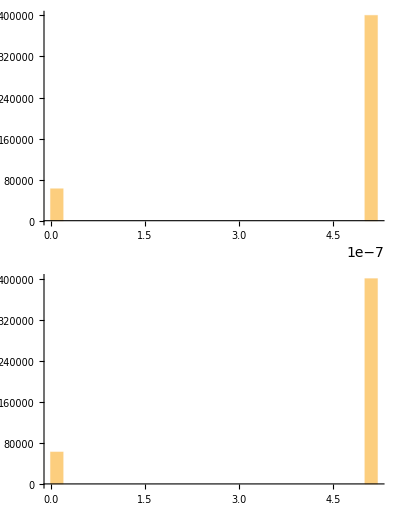

```mathematica
GraphicsGrid[{Histogram[ListConvolve[{1,-1},First/@#,PlotRange->All]]}&/@timeseries]
```

```mathematica
timestep=Mean[Median[ListConvolve[{1,-1},First/@#]]&/@timeseries]
```

5.×10^-7

### Display

```mathematica
ListPlot[Take[#,{55000,155000}]&/@timeseries,Frame->True,Joined->True]
```

-Graphics-

## Digitize time series

```mathematica
Dimensions[digitized=Map[{#⟦1⟧,HeavisideTheta[#⟦2⟧-3.0001]}&,timeseries,{2}]]
```

{2,524288,2}

### Display

```mathematica
ListPlot[Take[#,{55000,155000}]&/@digitized,Frame->True,Joined->True]
```

-Graphics-

#### Display complementary phases

```mathematica
ListPlot[MapThread[Function[{series, offset},#+{0,offset}&/@series],{digitized,{0,-1.2}}],Frame->True,Joined->True,PlotRange->All,FrameLabel->{"t [s]",""}]
```

-Graphics-

The data sent repeats every 50ms

#### Display one 50ms data transmission

```mathematica
ListPlot[Take[#,{255000,355000}]&/@MapThread[Function[{series, offset},#+{0,offset}&/@series],{digitized,{0,-1.2}}],Frame->True,Joined->True,PlotRange->All,FrameLabel->{"t [s]",""}]
```

-Graphics-

### Difference of time series

The zeros show where the phases do not overlap

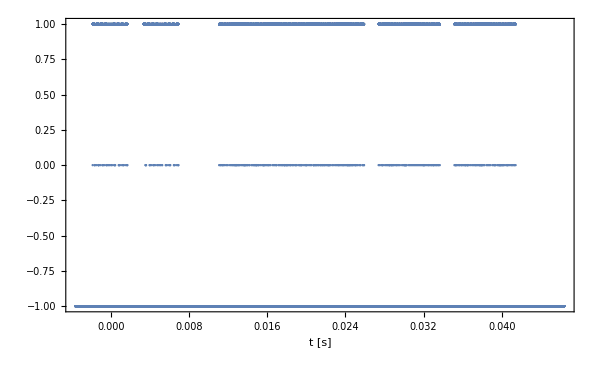

```mathematica
ListPlot[Take[MapThread[{(#1⟦1⟧+#2⟦1⟧)/2,#1⟦2⟧-#2⟦2⟧}&,digitized],{255000,355000}],Frame->True,Joined->False,PlotRange->All,FrameLabel->{"t [s]",""}]
```

#### Runs of identical values for difference series

```mathematica
Dimensions/@(diffruns=SplitBy[Take[MapThread[{(#1⟦1⟧+#2⟦1⟧)/2,#1⟦2⟧-#2⟦2⟧}&,digitized],{255000,355000}],Last])
```

{{3497,2},{1,2},{363,2},{1,2},{51,2},{51,2},{2,2},{362,2},{1,2},{361,2},{2,2},{51,2},{1,2},{51,2},{1,2},{361,2},{1,2},{362,2},{1,2},{51,2},{51,2},{2,2},{362,2},{1,2},{361,2},{1,2},{51,2},{1,2},{51,2},{1,2},{361,2},{1,2},{51,2},{1,2},{362,2},{51,2},{2,2},{361,2},{1,2},{361,2},{2,2},{50,2},{1,2},{52,2},{1,2},{362,2},{362,2},{1,2},{51,2},{1,2},{50,2},{2,2},{361,2},{1,2},{362,2},{1,2},{52,2},{52,2},{2,2},{362,2},{1,2},{361,2},{1,2},{51,2},{1,2},{51,2},{1,2},{3347,2},{362,2},{1,2},{51,2},{1,2},{50,2},{2,2},{362,2},{363,2},{1,2},{51,2},{51,2},{2,2},{362,2},{1,2},{361,2},{1,2},{51,2},{1,2},{51,2},{1,2},{361,2},{1,2},{362,2},{1,2},{51,2},{51,2},{1,2},{362,2},{1,2},{52,2},{1,2},{361,2},{1,2},{51,2},{1,2},{362,2},{362,2},{1,2},{51,2},{1,2},{51,2},{1,2},{362,2},{1,2},{361,2},{2,2},{51,2},{52,2},{1,2},{362,2},{362,2},{1,2},{52,2},{1,2},{51,2},{1,2},{361,2},{1,2},{362,2},{1,2},{50,2},{1,2},{51,2},{1,2},{8329,2},{1,2},{199,2},{1,2},{100,2},{1,2},{199,2},{1,2},{199,2},{1,2},{99,2},{2,2},{199,2},{100,2},{1,2},{97,2},{197,2},{1,2},{197,2},{1,2},{197,2},{1,2},{197,2},{198,2},{1,2},{197,2},{1,2},{196,2},{1,2},{198,2},{1,2},{99,2},{1,2},{100,2},{100,2},{1,2},{99,2},{1,2},{99,2},{1,2},{99,2},{1,2},{98,2},{2,2},{97,2},{1,2},{198,2},{1,2},{100,2},{1,2},{96,2},{1,2},{199,2},{1,2},{99,2},{1,2},{98,2},{197,2},{1,2},{196,2},{1,2},{199,2},{1,2},{100,2},{1,2},{98,2},{2,2},{99,2},{1,2},{100,2},{1,2},{99,2},{1,2},{97,2},{1,2},{198,2},{1,2},{99,2},{1,2},{98,2},{197,2},{2,2},{196,2},{199,2},{1,2},{100,2},{98,2},{1,2},{197,2},{1,2},{196,2},{2,2},{199,2},{1,2},{99,2},{1,2},{99,2},{1,2},{99,2},{2,2},{97,2},{1,2},{199,2},{1,2},{99,2},{1,2},{97,2},{1,2},{200,2},{100,2},{1,2},{97,2},{198,2},{1,2},{198,2},{1,2},{98,2},{2,2},{99,2},{1,2},{100,2},{1,2},{97,2},{1,2},{196,2},{1,2},{197,2},{1,2},{199,2},{1,2},{99,2},{1,2},{98,2},{1,2},{197,2},{1,2},{196,2},{1,2},{198,2},{198,2},{1,2},{197,2},{1,2},{197,2},{1,2},{197,2},{1,2},{197,2},{2,2},{197,2},{198,2},{1,2},{197,2},{1,2},{196,2},{1,2},{196,2},{1,2},{196,2},{2,2},{199,2},{99,2},{1,2},{100,2},{1,2},{99,2},{2,2},{97,2},{1,2},{198,2},{1,2},{100,2},{1,2},{96,2},{2,2},{196,2},{1,2},{199,2},{1,2},{99,2},{100,2},{1,2},{100,2},{1,2},{97,2},{1,2},{200,2},{100,2},{1,2},{100,2},{1,2},{199,2},{1,2},{99,2},{199,2},{2,2},{199,2},{1,2},{99,2},{1,2},{200,2},{200,2},{1,2},{99,2},{1,2},{199,2},{2,2},{199,2},{1,2},{99,2},{2,2},{201,2},{200,2},{1,2},{99,2},{199,2},{2,2},{198,2},{1,2},{99,2},{2,2},{198,2},{100,2},{1,2},{98,2},{198,2},{1,2},{197,2},{1,2},{197,2},{1,2},{198,2},{199,2},{2,2},{99,2},{1,2},{98,2},{1,2},{199,2},{1,2},{99,2},{1,2},{97,2},{1,2},{197,2},{1,2},{198,2},{1,2},{100,2},{1,2},{98,2},{196,2},{2,2},{196,2},{1,2},{196,2},{2,2},{196,2},{1,2},{196,2},{2,2},{196,2},{1,2},{197,2},{1,2},{197,2},{1,2},{199,2},{2,2},{99,2},{1,2},{100,2},{1,2},{99,2},{1,2},{100,2},{1,2},{100,2},{98,2},{1,2},{198,2},{197,2},{2,2},{197,2},{197,2},{1,2},{197,2},{1,2},{197,2},{1,2},{196,2},{1,2},{196,2},{2,2},{196,2},{1,2},{197,2},{1,2},{196,2},{1,2},{199,2},{1,2},{99,2},{1,2},{97,2},{1,2},{197,2},{1,2},{197,2},{1,2},{196,2},{1,2},{198,2},{2,2},{99,2},{1,2},{100,2},{1,2},{99,2},{1,2},{97,2},{2,2},{198,2},{1,2},{99,2},{1,2},{97,2},{1,2},{197,2},{2,2},{196,2},{1,2},{199,2},{1,2},{198,2},{1,2},{98,2},{2,2},{198,2},{1,2},{199,2},{1,2},{100,2},{199,2},{1,2},{199,2},{1,2},{100,2},{1,2},{199,2},{199,2},{1,2},{98,2},{1,2},{195,2},{2,2},{2991,2},{1,2},{199,2},{1,2},{100,2},{200,2},{1,2},{199,2},{1,2},{99,2},{2,2},{199,2},{100,2},{1,2},{98,2},{198,2},{1,2},{197,2},{1,2},{196,2},{1,2},{197,2},{1,2},{199,2},{2,2},{99,2},{1,2},{98,2},{1,2},{199,2},{1,2},{99,2},{2,2},{97,2},{1,2},{197,2},{2,2},{199,2},{100,2},{1,2},{97,2},{197,2},{2,2},{196,2},{1,2},{196,2},{1,2},{197,2},{1,2},{196,2},{1,2},{197,2},{197,2},{1,2},{197,2},{1,2},{198,2},{1,2},{100,2},{1,2},{99,2},{2,2},{99,2},{1,2},{98,2},{2,2},{99,2},{1,2},{98,2},{1,2},{197,2},{197,2},{1,2},{196,2},{1,2},{197,2},{1,2},{197,2},{1,2},{197,2},{1,2},{197,2},{1,2},{196,2},{1,2},{196,2},{1,2},{197,2},{1,2},{196,2},{1,2},{199,2},{1,2},{100,2},{98,2},{1,2},{196,2},{1,2},{196,2},{1,2},{197,2},{1,2},{198,2},{2,2},{98,2},{1,2},{100,2},{1,2},{98,2},{1,2},{97,2},{1,2},{199,2},{100,2},{1,2},{98,2},{197,2},{2,2},{196,2},{1,2},{199,2},{1,2},{199,2},{1,2},{100,2},{1,2},{199,2},{1,2},{199,2},{2,2},{99,2},{1,2},{199,2},{1,2},{198,2},{1,2},{100,2},{1,2},{199,2},{1,2},{198,2},{1,2},{100,2},{1,2},{195,2},{1,2},{2990,2},{1,2},{199,2},{2,2},{98,2},{1,2},{198,2},{2,2},{199,2},{100,2},{1,2},{199,2},{1,2},{100,2},{1,2},{98,2},{197,2},{2,2},{196,2},{1,2},{197,2},{1,2},{197,2},{1,2},{199,2},{2,2},{99,2},{1,2},{98,2},{1,2},{199,2},{1,2},{99,2},{2,2},{97,2},{1,2},{197,2},{1,2},{200,2},{100,2},{1,2},{98,2},{197,2},{1,2},{197,2},{1,2},{197,2},{1,2},{196,2},{1,2},{196,2},{2,2},{196,2},{1,2},{197,2},{1,2},{196,2},{1,2},{199,2},{2,2},{99,2},{1,2},{100,2},{1,2},{99,2},{1,2},{99,2},{2,2},{98,2},{1,2},{97,2},{1,2},{196,2},{1,2},{197,2},{1,2},{198,2},{197,2},{1,2},{197,2},{1,2},{197,2},{1,2},{196,2},{1,2},{196,2},{1,2},{197,2},{197,2},{1,2},{196,2},{1,2},{199,2},{1,2},{99,2},{1,2},{97,2},{2,2},{197,2},{197,2},{1,2},{197,2},{1,2},{198,2},{2,2},{99,2},{1,2},{100,2},{1,2},{99,2},{1,2},{97,2},{2,2},{198,2},{1,2},{99,2},{1,2},{97,2},{1,2},{197,2},{2,2},{197,2},{199,2},{1,2},{198,2},{1,2},{98,2},{2,2},{198,2},{1,2},{199,2},{1,2},{100,2},{199,2},{1,2},{198,2},{1,2},{100,2},{1,2},{199,2},{1,2},{199,2},{1,2},{100,2},{1,2},{196,2},{1,2},{9960,2}}

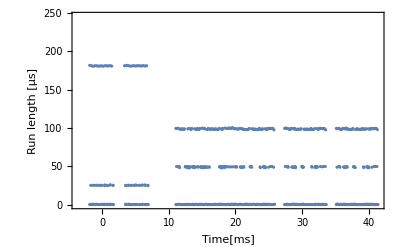

```mathematica
ListPlot[{10^3 First[First[#]],10^6 timestep Length[#]}&/@diffruns,Frame->True,FrameLabel->{"Time[ms]","Run length [μs]"}]
```

In the difference series, the short run lengths of the phase non-overlaps are visible.

#### Runs of identical values for each series

```mathematica
Map[Dimensions,runs=SplitBy[Take[#,{255000,355000}],Last]&/@digitized,{2}]
```

{{{3497,2},{365,2},{51,2},{53,2},{362,2},{364,2},{51,2},{53,2},{361,2},{364,2},{51,2},{53,2},{362,2},{363,2},{51,2},{53,2},{361,2},{53,2},{362,2},{53,2},{361,2},{364,2},{50,2},{54,2},{362,2},{363,2},{51,2},{53,2},{361,2},{364,2},{52,2},{54,2},{362,2},{363,2},{51,2},{53,2},{3347,2},{363,2},{51,2},{53,2},{362,2},{364,2},{51,2},{53,2},{362,2},{363,2},{51,2},{53,2},{361,2},{364,2},{51,2},{52,2},{362,2},{54,2},{361,2},{53,2},{362,2},{363,2},{51,2},{53,2},{362,2},{364,2},{51,2},{53,2},{362,2},{363,2},{52,2},{53,2},{361,2},{364,2},{50,2},{53,2},{8329,2},{201,2},{100,2},{201,2},{199,2},{102,2},{199,2},{101,2},{97,2},{198,2},{197,2},{199,2},{197,2},{199,2},{197,2},{198,2},{198,2},{101,2},{100,2},{101,2},{99,2},{101,2},{99,2},{101,2},{97,2},{200,2},{100,2},{98,2},{199,2},{101,2},{98,2},{198,2},{196,2},{201,2},{100,2},{101,2},{99,2},{102,2},{99,2},{99,2},{198,2},{101,2},{98,2},{199,2},{196,2},{200,2},{100,2},{99,2},{197,2},{199,2},{199,2},{101,2},{99,2},{102,2},{97,2},{201,2},{99,2},{99,2},{200,2},{101,2},{97,2},{199,2},{198,2},{101,2},{99,2},{102,2},{97,2},{198,2},{197,2},{201,2},{99,2},{100,2},{197,2},{198,2},{198,2},{199,2},{197,2},{199,2},{197,2},{200,2},{197,2},{199,2},{197,2},{198,2},{196,2},{199,2},{199,2},{100,2},{100,2},{102,2},{97,2},{200,2},{100,2},{99,2},{196,2},{201,2},{99,2},{101,2},{100,2},{99,2},{200,2},{101,2},{100,2},{201,2},{99,2},{201,2},{199,2},{101,2},{200,2},{201,2},{99,2},{202,2},{199,2},{102,2},{201,2},{201,2},{99,2},{201,2},{198,2},{102,2},{198,2},{101,2},{98,2},{199,2},{197,2},{199,2},{198,2},{201,2},{99,2},{100,2},{199,2},{101,2},{97,2},{199,2},{198,2},{102,2},{98,2},{198,2},{196,2},{199,2},{196,2},{199,2},{196,2},{199,2},{197,2},{202,2},{99,2},{102,2},{99,2},{102,2},{100,2},{99,2},{198,2},{199,2},{197,2},{198,2},{197,2},{199,2},{196,2},{199,2},{196,2},{199,2},{196,2},{201,2},{99,2},{99,2},{197,2},{199,2},{196,2},{201,2},{99,2},{102,2},{99,2},{100,2},{198,2},{101,2},{97,2},{200,2},{196,2},{201,2},{198,2},{101,2},{198,2},{201,2},{100,2},{200,2},{199,2},{102,2},{199,2},{200,2},{98,2},{198,2},{2991,2},{201,2},{100,2},{201,2},{199,2},{102,2},{199,2},{101,2},{98,2},{199,2},{197,2},{198,2},{197,2},{202,2},{99,2},{100,2},{199,2},{102,2},{97,2},{200,2},{199,2},{101,2},{97,2},{199,2},{196,2},{198,2},{197,2},{198,2},{197,2},{198,2},{197,2},{200,2},{100,2},{102,2},{99,2},{101,2},{99,2},{100,2},{197,2},{198,2},{196,2},{199,2},{197,2},{199,2},{197,2},{198,2},{196,2},{199,2},{196,2},{201,2},{100,2},{99,2},{196,2},{198,2},{197,2},{201,2},{98,2},{102,2},{98,2},{99,2},{199,2},{101,2},{98,2},{199,2},{196,2},{201,2},{199,2},{102,2},{199,2},{202,2},{99,2},{201,2},{198,2},{102,2},{199,2},{200,2},{100,2},{197,2},{2990,2},{202,2},{98,2},{201,2},{199,2},{101,2},{199,2},{102,2},{98,2},{199,2},{196,2},{199,2},{197,2},{202,2},{99,2},{100,2},{199,2},{102,2},{97,2},{199,2},{200,2},{101,2},{98,2},{198,2},{197,2},{199,2},{196,2},{199,2},{196,2},{199,2},{196,2},{202,2},{99,2},{102,2},{99,2},{102,2},{98,2},{99,2},{196,2},{199,2},{198,2},{198,2},{197,2},{199,2},{196,2},{198,2},{197,2},{198,2},{196,2},{201,2},{99,2},{100,2},{197,2},{198,2},{197,2},{201,2},{99,2},{102,2},{99,2},{100,2},{198,2},{101,2},{97,2},{200,2},{197,2},{200,2},{198,2},{101,2},{198,2},{201,2},{100,2},{200,2},{198,2},{102,2},{199,2},{201,2},{100,2},{198,2},{9960,2}},{{3498,2},{363,2},{52,2},{51,2},{365,2},{361,2},{54,2},{51,2},{363,2},{362,2},{52,2},{51,2},{365,2},{361,2},{53,2},{51,2},{363,2},{51,2},{363,2},{51,2},{364,2},{361,2},{53,2},{52,2},{363,2},{362,2},{53,2},{50,2},{364,2},{362,2},{53,2},{52,2},{365,2},{361,2},{53,2},{51,2},{3348,2},{362,2},{53,2},{50,2},{364,2},{363,2},{52,2},{51,2},{365,2},{361,2},{53,2},{51,2},{363,2},{362,2},{52,2},{51,2},{364,2},{52,2},{363,2},{51,2},{363,2},{362,2},{53,2},{51,2},{364,2},{361,2},{53,2},{52,2},{363,2},{362,2},{54,2},{51,2},{363,2},{362,2},{52,2},{51,2},{8331,2},{199,2},{102,2},{199,2},{201,2},{99,2},{201,2},{100,2},{98,2},{197,2},{199,2},{197,2},{198,2},{198,2},{199,2},{196,2},{200,2},{99,2},{101,2},{100,2},{101,2},{99,2},{101,2},{98,2},{100,2},{198,2},{102,2},{96,2},{201,2},{99,2},{99,2},{197,2},{198,2},{199,2},{102,2},{98,2},{102,2},{100,2},{101,2},{97,2},{200,2},{99,2},{99,2},{197,2},{198,2},{199,2},{101,2},{98,2},{199,2},{196,2},{202,2},{99,2},{101,2},{99,2},{100,2},{199,2},{101,2},{97,2},{201,2},{100,2},{98,2},{198,2},{200,2},{98,2},{102,2},{100,2},{99,2},{196,2},{199,2},{199,2},{101,2},{98,2},{199,2},{196,2},{199,2},{198,2},{199,2},{197,2},{199,2},{197,2},{199,2},{198,2},{199,2},{196,2},{198,2},{196,2},{201,2},{99,2},{102,2},{99,2},{100,2},{198,2},{102,2},{96,2},{199,2},{199,2},{100,2},{100,2},{102,2},{97,2},{201,2},{100,2},{102,2},{199,2},{100,2},{199,2},{202,2},{99,2},{201,2},{200,2},{101,2},{199,2},{202,2},{99,2},{203,2},{200,2},{100,2},{199,2},{201,2},{99,2},{200,2},{100,2},{99,2},{198,2},{199,2},{197,2},{199,2},{199,2},{102,2},{98,2},{201,2},{99,2},{99,2},{197,2},{200,2},{100,2},{99,2},{196,2},{199,2},{196,2},{199,2},{196,2},{199,2},{197,2},{199,2},{199,2},{102,2},{100,2},{101,2},{100,2},{101,2},{98,2},{199,2},{197,2},{199,2},{197,2},{199,2},{197,2},{198,2},{196,2},{199,2},{197,2},{198,2},{199,2},{101,2},{97,2},{199,2},{197,2},{198,2},{198,2},{102,2},{100,2},{101,2},{97,2},{201,2},{99,2},{99,2},{197,2},{199,2},{199,2},{200,2},{98,2},{201,2},{199,2},{101,2},{199,2},{201,2},{100,2},{200,2},{199,2},{100,2},{195,2},{2994,2},{199,2},{101,2},{200,2},{201,2},{99,2},{201,2},{100,2},{99,2},{198,2},{199,2},{196,2},{199,2},{199,2},{102,2},{98,2},{201,2},{99,2},{100,2},{197,2},{201,2},{100,2},{98,2},{197,2},{199,2},{196,2},{199,2},{196,2},{198,2},{197,2},{199,2},{198,2},{102,2},{99,2},{102,2},{98,2},{102,2},{98,2},{198,2},{197,2},{198,2},{197,2},{199,2},{197,2},{199,2},{196,2},{198,2},{197,2},{198,2},{199,2},{101,2},{98,2},{198,2},{196,2},{199,2},{198,2},{101,2},{100,2},{100,2},{97,2},{200,2},{100,2},{99,2},{197,2},{199,2},{199,2},{201,2},{100,2},{201,2},{199,2},{102,2},{199,2},{200,2},{100,2},{201,2},{198,2},{102,2},{195,2},{2992,2},{199,2},{101,2},{198,2},{201,2},{100,2},{201,2},{100,2},{99,2},{197,2},{199,2},{197,2},{199,2},{199,2},{102,2},{98,2},{201,2},{99,2},{100,2},{197,2},{201,2},{100,2},{99,2},{197,2},{199,2},{197,2},{198,2},{196,2},{199,2},{197,2},{198,2},{199,2},{102,2},{100,2},{101,2},{99,2},{101,2},{97,2},{198,2},{197,2},{199,2},{197,2},{199,2},{197,2},{198,2},{196,2},{198,2},{197,2},{198,2},{199,2},{101,2},{97,2},{199,2},{197,2},{199,2},{198,2},{102,2},{100,2},{101,2},{97,2},{201,2},{99,2},{99,2},{197,2},{199,2},{199,2},{200,2},{98,2},{201,2},{199,2},{101,2},{199,2},{200,2},{100,2},{201,2},{199,2},{102,2},{196,2},{9961,2}}}

```mathematica
Length/@runs
```

{421,421}

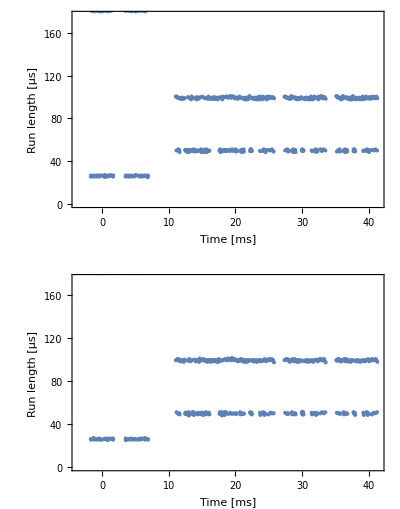

```mathematica
GraphicsGrid[{ListPlot[{10^3 First[First[#]],10^6 timestep Length[#]}&/@#,Frame->True,FrameLabel->{"Time [ms]","Run length [μs]"}]}&/@runs]
```

It is clearly apparent that the short modulation bursts have a different encoding timing than the remaining long and medium length bursts.

## Packets within the time series

### Short data packets

MM format, see 2.2.9 Einbettung von Steuerbefehlen im MM-Format

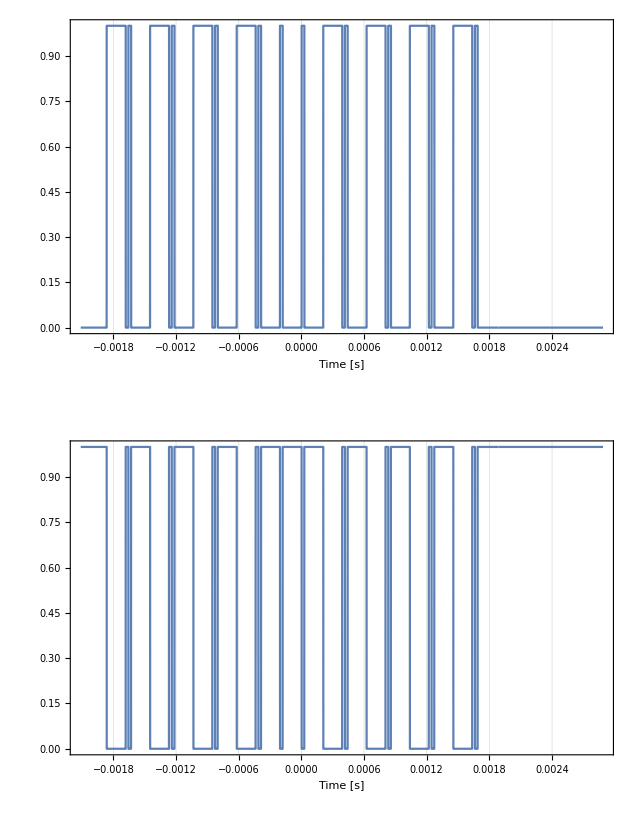

```mathematica
GraphicsGrid[{ListPlot[Take[#,{258000,268000}],Frame->True,Joined->True,FrameLabel->{"Time [s]",""},GridLines->{Range[-.15,.15,1.*^-4],None}]}&/@digitized]
```

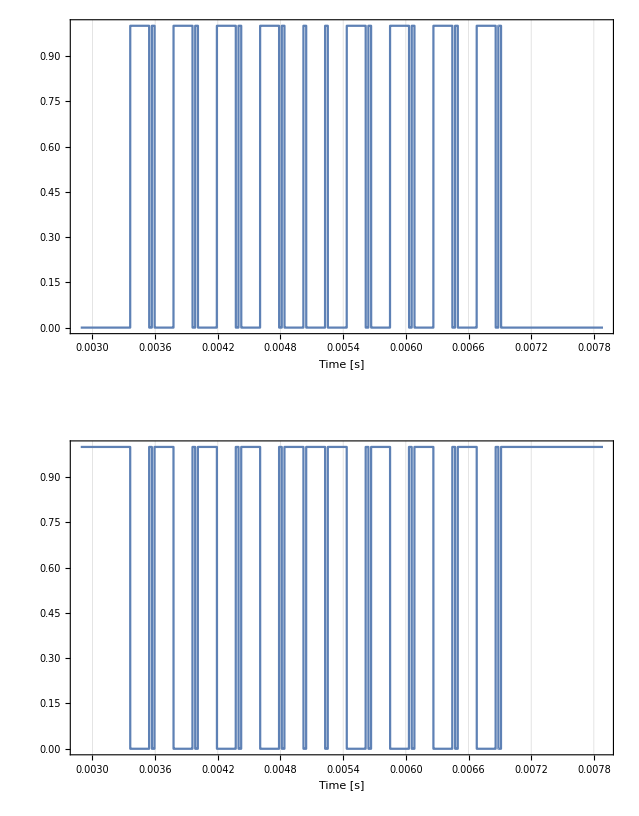

```mathematica
GraphicsGrid[{ListPlot[Take[#,{268000,278000}],Frame->True,Joined->True,FrameLabel->{"Time [s]",""},GridLines->{Range[-.15,.15,1.*^-4],None}]}&/@digitized]
```

### Medium length data packets

mfx signal

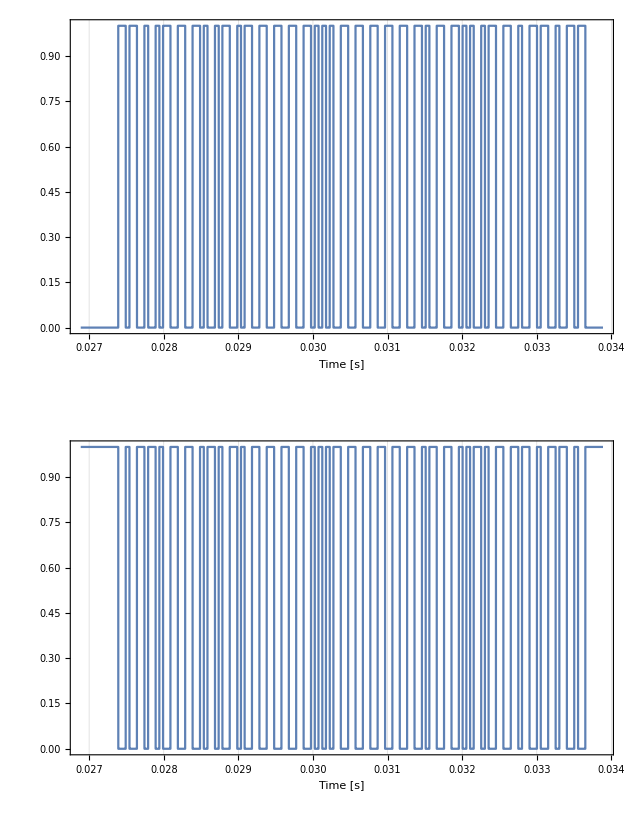

```mathematica
GraphicsGrid[{ListPlot[Take[#,{316000,330000}],Frame->True,Joined->True,FrameLabel->{"Time [s]",""},GridLines->{Range[-.15,.15,1.*^-4],None}]}&/@digitized]
```

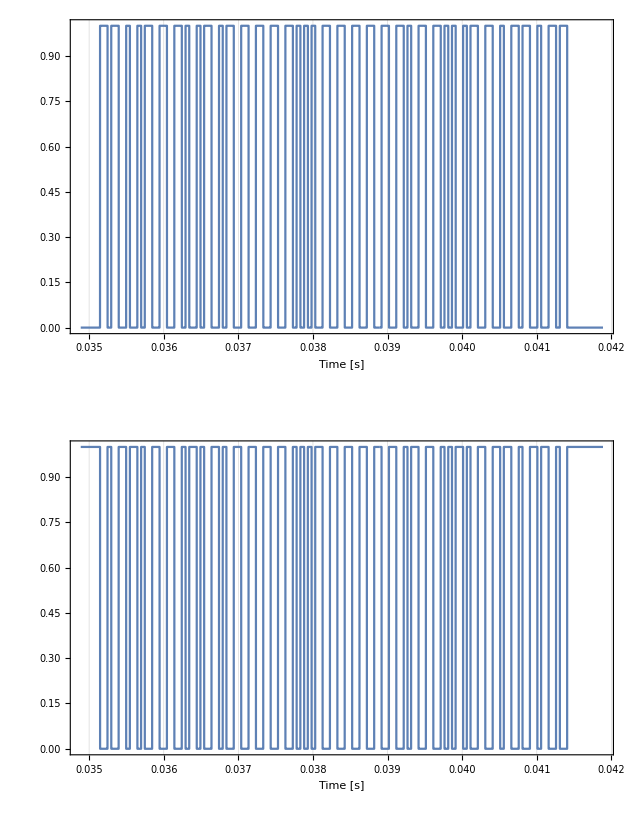

```mathematica
GraphicsGrid[{ListPlot[Take[#,{332000,346000}],Frame->True,Joined->True,FrameLabel->{"Time [s]",""},GridLines->{Range[-.15,.15,1.*^-4],None}]}&/@digitized]
```

manually:
SYNC, 7’A:5, drive fwd 7’0, func 16’ F3 on, CRC8’b01101000, SYNC, SYNC

### Long data packet

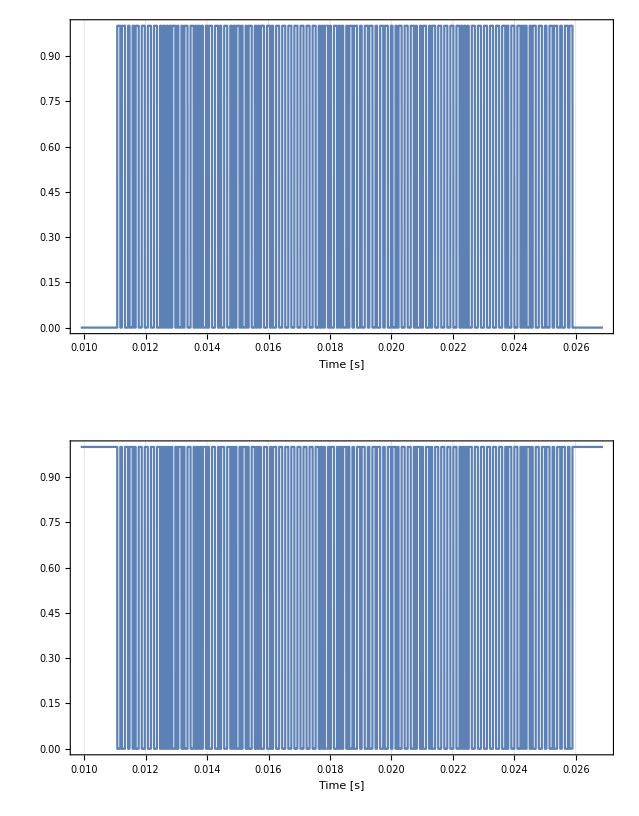

```mathematica
GraphicsGrid[{ListPlot[Take[#,{282000,316000}],Frame->True,Joined->True,FrameLabel->{"Time [s]",""},GridLines->{Range[-.15,.15,1.*^-4],None}]}&/@digitized]
```

## Run length decoding

#### bit frame (100μs) per sampling step

```mathematica
timestep/10^-4
```

0.005

#### Get run lengths of full traces

```mathematica
Length/@(fullruns=SplitBy[#,Last]&/@digitized)
```

{2312,2312}

### Run lengths in bit frames

```mathematica
rlbits=Map[timestep/10^-4 Length[#]&,fullruns,{2}]
```

{{0.275,0.995,0.51,0.48,1.,0.99,0.5,0.5,0.51,0.485,0.99,0.985,1.005,0.495,0.5,0.985,0.995,0.98,0.99,0.985,0.99,0.98,0.995,0.98,0.995,0.985,0.995,0.985,0.995,0.995,0.51,0.49,0.51,0.49,1.005,0.495,0.495,0.985,1.,0.495,0.51,0.495,0.5,0.995,0.505,0.495,1.005,0.5,1.,0.99,0.505,0.995,1.005,0.5,1.005,0.995,0.505,1.005,1.005,0.5,1.005,0.995,0.505,0.99,0.505,0.49,0.995,0.985,0.99,0.98,1.005,0.495,0.495,0.995,0.505,0.49,0.995,0.99,0.51,0.485,0.995,0.98,0.995,0.985,0.995,0.98,0.995,0.985,1.005,0.495,0.505,0.495,0.51,0.5,0.495,0.98,0.99,0.98,0.995,0.985,0.99,0.985,0.995,0.98,0.995,0.98,1.,0.495,0.495,0.985,0.995,0.985,1.,0.5,0.505,0.5,0.49,0.995,0.505,0.49,0.995,0.98,1.005,0.99,0.51,0.995,1.,0.495,1.005,0.995,0.51,0.995,1.005,0.5,0.99,14.95,1.005,0.495,1.005,0.995,0.505,0.995,0.505,0.48,0.995,0.985,0.99,0.985,1.005,0.5,0.5,0.995,0.505,0.485,0.995,0.99,0.51,0.485,0.995,0.98,0.995,0.98,0.995,0.985,0.995,0.98,1.005,0.49,0.51,0.495,0.51,0.5,0.495,0.985,0.995,0.985,0.995,0.98,0.995,0.985,0.99,0.985,0.99,0.985,1.005,0.495,0.495,0.985,0.995,0.98,1.01,0.495,0.505,0.5,0.495,0.995,0.51,0.485,0.99,0.99,1.005,0.99,0.505,0.995,1.01,0.495,1.,0.99,0.505,0.995,1.01,0.495,0.99,14.955,1.005,0.495,1.005,0.99,0.505,0.995,0.51,0.485,0.995,0.985,0.995,0.98,1.005,0.5,0.495,0.995,0.505,0.49,0.995,0.995,0.51,0.485,0.995,0.985,0.99,0.985,0.995,0.98,0.995,0.98,1.005,0.495,0.51,0.5,0.505,0.495,0.49,0.985,0.995,0.985,0.995,0.98,0.99,0.985,0.995,0.98,0.995,0.98,1.005,0.495,0.495,0.985,0.995,0.98,1.,0.5,0.51,0.495,0.495,0.995,0.5,0.49,0.995,0.985,1.,0.99,0.505,0.995,1.01,0.495,1.005,0.99,0.51,0.995,1.,0.495,0.99,54.78,1.815,0.255,0.265,1.805,1.825,0.255,0.265,1.81,1.82,0.255,0.265,1.805,1.82,0.255,0.265,1.81,0.265,1.805,0.265,1.815,1.82,0.255,0.265,1.805,1.82,0.255,0.265,1.805,1.825,0.25,0.27,1.81,1.82,0.255,0.27,16.745,1.815,0.255,0.265,1.81,1.82,0.26,0.26,1.81,1.82,0.255,0.27,1.81,1.82,0.255,0.265,1.81,0.265,1.805,0.265,1.81,1.815,0.255,0.265,1.805,1.82,0.255,0.265,1.81,1.82,0.255,0.265,1.805,1.82,0.255,0.265,41.645,1.005,0.495,1.005,0.995,0.51,0.99,0.505,0.485,1.,0.985,0.995,0.98,0.995,0.98,1.,0.995,0.51,0.495,0.51,0.495,0.51,0.5,0.505,0.49,1.005,0.49,0.495,0.995,0.51,0.48,0.99,0.985,1.,0.495,0.505,0.5,0.505,0.495,0.495,0.995,0.505,0.49,0.995,0.98,1.005,0.5,0.49,0.98,0.995,0.99,0.51,0.49,0.51,0.485,1.01,0.495,0.495,0.99,0.505,0.485,0.995,0.99,0.51,0.5,0.505,0.49,0.99,0.985,1.01,0.495,0.5,0.985,0.995,0.985,0.995,0.985,0.995,0.98,0.995,0.985,0.995,0.985,0.99,0.98,0.995,0.99,0.505,0.5,0.505,0.49,1.,0.5,0.49,0.985,1.01,0.49,0.51,0.5,0.495,0.99,0.51,0.49,1.005,0.495,1.01,0.995,0.505,0.99,1.01,0.495,1.,0.995,0.505,1.005,1.01,0.49,1.005,0.995,0.505,0.99,0.505,0.485,1.,0.98,0.995,0.98,1.005,0.5,0.49,0.995,0.505,0.49,0.995,0.99,0.51,0.485,0.99,0.98,0.99,0.985,0.995,0.98,0.99,0.98,1.005,0.495,0.505,0.495,0.51,0.495,0.5,0.98,0.99,0.98,0.995,0.985,0.99,0.985,0.995,0.98,0.995,0.98,1.,0.495,0.495,0.98,1.,0.985,1.005,0.495,0.505,0.5,0.495,0.995,0.51,0.49,0.995,0.98,1.,0.995,0.51,0.99,1.,0.5,1.005,0.99,0.51,0.995,1.005,0.5,0.985,14.95,1.005,0.495,1.01,0.995,0.5,0.995,0.51,0.485,0.995,0.98,0.995,0.98,1.005,0.495,0.5,0.995,0.505,0.485,0.995,0.99,0.51,0.485,0.995,0.985,0.99,0.98,0.995,0.985,0.995,0.985,1.,0.5,0.51,0.495,0.51,0.495,0.5,0.985,0.995,0.985,0.99,0.985,1.,0.98,0.99,0.98,0.99,0.985,1.005,0.49,0.5,0.985,0.99,0.985,1.01,0.495,0.505,0.495,0.5,0.99,0.505,0.485,0.995,0.985,1.005,0.99,0.5,0.995,1.005,0.495,1.,0.995,0.505,0.995,1.01,0.495,0.99,14.955,1.005,0.5,1.005,0.995,0.51,0.995,0.505,0.49,0.99,0.98,0.99,0.985,1.005,0.495,0.495,0.99,0.5,0.49,0.995,0.99,0.51,0.49,0.995,0.98,0.99,0.98,0.995,0.98,0.995,0.985,1.005,0.5,0.505,0.5,0.505,0.5,0.495,0.985,0.99,0.98,0.995,0.985,0.995,0.985,0.99,0.98,0.995,0.985,1.005,0.495,0.5,0.985,0.995,0.985,1.005,0.495,0.51,0.495,0.5,0.99,0.505,0.485,0.995,0.985,1.005,0.995,0.51,0.995,1.,0.49,1.01,0.995,0.505,0.995,1.005,0.495,0.99,54.78,1.815,0.255,0.265,1.805,1.82,0.25,0.265,1.81,1.82,0.255,0.265,1.81,1.82,0.255,0.265,1.81,0.265,1.81,0.27,1.81,1.815,0.255,0.265,1.805,1.82,0.26,0.26,1.81,1.82,0.255,0.27,1.805,1.825,0.255,0.26,16.735,1.815,0.255,0.265,1.805,1.82,0.26,0.265,1.81,1.82,0.255,0.265,1.805,1.82,0.25,0.27,1.81,0.26,1.81,0.27,1.805,1.82,0.25,0.27,1.81,1.815,0.255,0.265,1.805,1.82,0.25,0.265,1.815,1.815,0.26,0.265,41.635,1.005,0.5,1.,0.995,0.505,0.995,0.5,0.49,0.99,0.985,0.995,0.98,0.995,0.985,0.995,0.995,0.51,0.5,0.505,0.5,0.505,0.5,0.51,0.485,1.005,0.5,0.495,0.99,0.51,0.49,0.995,0.985,1.005,0.5,0.505,0.495,0.505,0.495,0.5,0.995,0.5,0.485,0.99,0.98,1.,0.495,0.5,0.985,0.995,0.995,0.51,0.49,0.51,0.49,1.005,0.495,0.495,0.995,0.505,0.485,0.995,0.995,0.5,0.5,0.51,0.485,0.995,0.985,1.005,0.495,0.495,0.985,0.995,0.98,1.,0.985,0.99,0.98,0.995,0.99,0.995,0.985,0.99,0.98,1.,0.995,0.505,0.5,0.505,0.49,1.005,0.5,0.49,0.985,1.,0.49,0.51,0.5,0.495,0.99,0.51,0.5,1.005,0.49,1.01,0.995,0.505,0.995,1.005,0.495,1.005,0.99,0.505,1.01,1.005,0.49,1.01,0.99,0.505,0.99,0.51,0.485,0.995,0.98,0.99,0.985,1.005,0.495,0.5,0.995,0.505,0.49,0.995,0.995,0.51,0.49,0.995,0.985,0.995,0.98,0.995,0.98,0.995,0.98,1.005,0.495,0.505,0.495,0.505,0.495,0.5,0.985,0.995,0.985,1.,0.985,0.995,0.985,0.995,0.98,0.995,0.985,1.005,0.495,0.5,0.985,0.995,0.98,1.005,0.495,0.505,0.495,0.5,0.995,0.505,0.48,1.,0.985,1.005,0.995,0.51,0.99,1.005,0.5,1.005,0.995,0.51,0.995,1.005,0.495,0.99,14.955,1.005,0.495,1.,0.995,0.505,0.995,0.51,0.485,1.,0.985,0.995,0.98,1.,0.5,0.495,0.995,0.505,0.48,1.,0.99,0.5,0.49,0.99,0.985,0.995,0.985,0.995,0.985,0.99,0.985,1.005,0.495,0.51,0.495,0.505,0.495,0.495,0.98,0.995,0.98,0.995,0.985,0.995,0.98,1.,0.985,0.99,0.98,1.,0.5,0.49,0.985,0.995,0.985,1.005,0.5,0.505,0.495,0.5,0.995,0.505,0.485,0.995,0.985,1.005,0.995,0.5,1.,1.005,0.5,1.,0.995,0.505,1.,1.005,0.495,0.985,14.955,1.005,0.5,1.005,0.995,0.51,0.995,0.5,0.485,0.995,0.98,1.,0.98,1.005,0.49,0.5,0.99,0.505,0.485,0.995,0.99,0.505,0.49,0.995,0.985,0.99,0.985,1.,0.985,0.995,0.98,1.,0.5,0.5,0.495,0.505,0.49,0.5,0.985,0.995,0.98,0.995,0.99,0.995,0.985,0.99,0.98,0.995,0.985,1.005,0.495,0.5,0.985,0.995,0.98,1.005,0.495,0.505,0.5,0.495,0.99,0.51,0.485,1.,0.985,1.005,0.99,0.505,0.995,1.005,0.5,1.005,0.995,0.51,0.995,1.005,0.5,0.99,54.775,1.825,0.255,0.265,1.81,1.82,0.255,0.265,1.805,1.82,0.255,0.265,1.81,1.815,0.255,0.265,1.805,0.265,1.81,0.265,1.805,1.82,0.25,0.27,1.81,1.815,0.255,0.265,1.805,1.82,0.26,0.27,1.81,1.815,0.255,0.265,16.735,1.815,0.255,0.265,1.81,1.82,0.255,0.265,1.81,1.815,0.255,0.265,1.805,1.82,0.255,0.26,1.81,0.27,1.805,0.265,1.81,1.815,0.255,0.265,1.81,1.82,0.255,0.265,1.81,1.815,0.26,0.265,1.805,1.82,0.25,0.265,41.645,1.005,0.5,1.005,0.995,0.51,0.995,0.505,0.485,0.99,0.985,0.995,0.985,0.995,0.985,0.99,0.99,0.505,0.5,0.505,0.495,0.505,0.495,0.505,0.485,1.,0.5,0.49,0.995,0.505,0.49,0.99,0.98,1.005,0.5,0.505,0.495,0.51,0.495,0.495,0.99,0.505,0.49,0.995,0.98,1.,0.5,0.495,0.985,0.995,0.995,0.505,0.495,0.51,0.485,1.005,0.495,0.495,1.,0.505,0.485,0.995,0.99,0.505,0.495,0.51,0.485,0.99,0.985,1.005,0.495,0.5,0.985,0.99,0.99,0.995,0.985,0.995,0.985,1.,0.985,0.995,0.985,0.99,0.98,0.995,0.995,0.5,0.5,0.51,0.485,1.,0.5,0.495,0.98,1.005,0.495,0.505,0.5,0.495,1.,0.505,0.5,1.005,0.495,1.005,0.995,0.505,1.,1.005,0.495,1.01,0.995,0.51,1.005,1.005,0.495,1.005,0.99,0.51,0.99,0.505,0.49,0.995,0.985,0.995,0.99,1.005,0.495,0.5,0.995,0.505,0.485,0.995,0.99,0.51,0.49,0.99,0.98,0.995,0.98,0.995,0.98,0.995,0.985,1.01,0.495,0.51,0.495,0.51,0.5,0.495,0.99,0.995,0.985,0.99,0.985,0.995,0.98,0.995,0.98,0.995,0.98,1.005,0.495,0.495,0.985,0.995,0.98,1.005,0.495,0.51,0.495,0.5,0.99,0.505,0.485,1.,0.98,1.005,0.99,0.505,0.99,1.005,0.5,1.,0.995,0.51,0.995,1.,0.49,0.99,14.955,1.005,0.5,1.005,0.995,0.51,0.995,0.505,0.49,0.995,0.985,0.99,0.985,1.01,0.495,0.5,0.995,0.51,0.485,1.,0.995,0.505,0.485,0.995,0.98,0.99,0.985,0.99,0.985,0.99,0.985,1.,0.5,0.51,0.495,0.505,0.495,0.5,0.985,0.99,0.98,0.995,0.985,0.995,0.985,0.99,0.98,0.995,0.98,1.005,0.5,0.495,0.98,0.99,0.985,1.005,0.49,0.51,0.49,0.495,0.995,0.505,0.49,0.995,0.98,1.005,0.995,0.51,0.995,1.01,0.495,1.005,0.99,0.51,0.995,1.,0.5,0.985,14.95,1.01,0.49,1.005,0.995,0.505,0.995,0.51,0.49,0.995,0.98,0.995,0.985,1.01,0.495,0.5,0.995,0.51,0.485,0.995,1.,0.505,0.49,0.99,0.985,0.995,0.98,0.995,0.98,0.995,0.98,1.01,0.495,0.51,0.495,0.51,0.49,0.495,0.98,0.995,0.99,0.99,0.985,0.995,0.98,0.99,0.985,0.99,0.98,1.005,0.495,0.5,0.985,0.99,0.985,1.005,0.495,0.51,0.495,0.5,0.99,0.505,0.485,1.,0.985,1.,0.99,0.505,0.99,1.005,0.5,1.,0.99,0.51,0.995,1.005,0.5,0.99,54.785,1.815,0.255,0.27,1.805,1.82,0.255,0.27,1.81,1.815,0.255,0.265,1.805,1.82,0.26,0.265,1.81,0.265,1.81,0.265,1.81,1.815,0.255,0.265,1.81,1.82,0.255,0.265,1.81,1.815,0.255,0.27,1.805,1.82,0.255,0.265,16.735,1.82,0.255,0.265,1.81,1.82,0.26,0.26,1.81,1.815,0.255,0.265,1.81,1.82,0.255,0.26,1.81,0.265,1.805,0.265,1.805,1.82,0.255,0.27,1.805,1.82,0.25,0.265,1.81,1.815,0.26,0.265,1.81,1.82,0.255,0.265,41.645,1.005,0.5,1.005,0.995,0.51,0.995,0.505,0.485,0.995,0.98,0.995,0.98,0.995,0.985,0.995,0.99,0.51,0.495,0.505,0.49,0.505,0.5,0.505,0.49,1.005,0.49,0.495,0.995,0.505,0.48,1.,0.98,1.,0.5,0.505,0.5,0.505,0.495,0.49,0.995,0.505,0.49,0.995,0.98,1.005,0.5,0.49,0.98,0.995,0.99,0.505,0.495,0.51,0.485,1.01,0.495,0.5,0.995,0.505,0.49,0.995,0.99,0.505,0.5,0.505,0.49,0.995,0.98,1.01,0.495,0.495,0.985,0.995,0.98,0.99,0.985,0.995,0.985,0.995,0.98,0.99,0.99,0.995,0.985,0.995,0.995,0.51,0.5,0.505,0.485,1.005,0.5,0.495,0.985,1.005,0.5,0.505,0.495,0.5,0.995,0.51,0.495,1.005,0.5,1.,0.99,0.505,0.995,1.,0.5,1.005,0.99,0.505,1.005,1.005,0.5,1.,0.995,0.51,0.99,0.51,0.485,0.995,0.985,0.995,0.985,1.01,0.49,0.5,0.995,0.51,0.485,0.99,0.995,0.5,0.49,0.99,0.985,0.995,0.985,0.995,0.985,0.99,0.985,1.005,0.5,0.51,0.495,0.51,0.495,0.5,0.985,0.995,0.99,0.995,0.985,0.995,0.985,0.995,0.985,0.995,0.98,1.,0.5,0.49,0.99,0.99,0.985,1.,0.5,0.505,0.5,0.49,1.,0.505,0.49,0.995,0.985,1.005,1.,0.505,0.995,1.005,0.5,1.005,0.995,0.51,0.995,1.005,0.5,0.99,14.95,1.005,0.5,1.005,0.99,0.505,0.995,0.505,0.49,0.995,0.98,0.995,0.985,1.01,0.495,0.5,0.99,0.51,0.485,0.995,0.995,0.505,0.49,0.995,0.985,0.995,0.98,1.,0.98,0.99,0.98,1.005,0.495,0.505,0.495,0.505,0.495,0.5,0.985,0.995,0.985,1.,0.985,0.995,0.985,0.995,0.98,0.99,0.985,1.,0.495,0.495,0.985,0.995,0.98,1.01,0.495,0.505,0.495,0.5,0.995,0.505,0.485,0.995,0.985,1.005,0.99,0.51,0.995,1.,0.49,1.01,0.995,0.505,0.99,1.005,0.495,0.99,14.955,1.01,0.495,1.005,0.995,0.505,0.995,0.51,0.485,0.99,0.985,1.,0.98,1.005,0.5,0.49,0.995,0.51,0.485,0.995,0.99,0.51,0.485,0.99,0.99,0.995,0.98,0.99,0.985,0.99,0.985,1.005,0.5,0.505,0.5,0.505,0.5,0.495,0.985,0.995,0.985,0.995,0.985,0.995,0.98,0.995,0.98,0.995,0.985,1.005,0.5,0.495,0.98,0.995,0.98,1.005,0.5,0.505,0.5,0.495,0.995,0.505,0.485,0.99,0.985,1.,0.99,0.505,0.995,1.01,0.495,1.005,0.995,0.5,1.,1.005,0.49,0.99,54.78,1.815,0.255,0.265,1.805,1.82,0.26,0.265,1.81,1.82,0.25,0.265,1.81,1.815,0.26,0.265,1.805,0.27,1.805,0.265,1.81,1.815,0.255,0.27,1.805,1.82,0.255,0.26,1.81,1.815,0.255,0.27,1.81,1.82,0.255,0.265,16.74,1.82,0.255,0.265,1.805,1.82,0.25,0.27,1.81,1.815,0.255,0.265,1.81,1.82,0.25,0.265,1.81,0.265,1.81,0.265,1.81,1.82,0.25,0.265,1.805,1.82,0.255,0.26,1.81,1.82,0.255,0.265,1.81,1.82,0.255,0.26,41.645,1.01,0.495,1.005,0.995,0.505,0.995,0.51,0.485,0.99,0.985,0.995,0.985,0.99,0.98,0.995,0.99,0.505,0.495,0.505,0.495,0.51,0.495,0.51,0.485,1.,0.495,0.49,0.99,0.505,0.49,0.995,0.98,1.005,0.495,0.51,0.495,0.51,0.49,0.495,0.995,0.51,0.48,0.99,0.98,1.005,0.495,0.495,0.985,0.99,0.995,0.51,0.5,0.505,0.49,1.,0.5,0.495,0.995,0.51,0.49,0.99,0.995,0.51,0.495,0.505,0.485,0.995,0.985,1.005,0.495,0.5,0.98,0.995,0.98,0.995,0.985,0.995,0.98,1.,0.985,0.995,0.98,0.995,0.985,0.99,0.995,0.5,0.5,0.505,0.485,1.,0.495,0.5,0.98,1.005,0.495,0.505,0.5,0.495,0.995,0.505,0.495,1.005,0.495,1.,0.995,0.505,0.99,1.005,0.495,1.005,1.,0.505,1.,1.01,0.495,1.,0.995,0.505,0.99,0.51,0.485,1.,0.985,0.995,0.98,1.005,0.495,0.5,0.995,0.505,0.49,0.99,0.99,0.505,0.485,1.,0.98,0.995,0.985,0.995,0.985,0.995,0.98,1.,0.495,0.51,0.495,0.505,0.495,0.495,0.98,0.995,0.98,0.995,0.98,0.99,0.985,0.99,0.985,0.99,0.98,1.005,0.5,0.495,0.985,0.995,0.985,1.005,0.5,0.51,0.495,0.5,0.995,0.505,0.485,0.995,0.985,1.005,0.995,0.505,0.995,1.005,0.49,1.005,0.995,0.51,0.99,1.,0.5,0.99,14.955,1.005,0.5,1.005,0.995,0.51,0.99,0.505,0.49,0.995,0.985,0.995,0.98,1.,0.5,0.495,0.995,0.505,0.49,0.995,0.995,0.51,0.485,0.99,0.99,0.995,0.98,0.995,0.985,1.,0.98,1.005,0.495,0.505,0.5,0.51,0.495,0.5,0.985,0.99,0.985,0.99,0.985,0.995,0.985,0.99,0.985,0.995,0.985,1.,0.495,0.495,0.98,0.995,0.985,1.005,0.495,0.51,0.495,0.5,0.99,0.51,0.48,0.99,0.985,1.005,0.995,0.505,0.995,1.,0.495,1.005,0.995,0.505,0.99,1.005,0.295},{0.27,1.005,0.5,0.49,0.985,1.,0.495,0.51,0.495,0.5,0.98,0.99,0.995,0.51,0.49,0.995,0.985,0.99,0.98,0.99,0.98,0.995,0.985,0.99,0.98,0.995,0.99,0.995,0.985,1.005,0.5,0.5,0.5,0.495,1.,0.5,0.49,0.995,0.99,0.505,0.495,0.51,0.485,1.01,0.49,0.51,0.995,0.505,0.995,1.,0.49,1.01,0.995,0.505,1.,1.005,0.495,1.015,0.995,0.505,0.995,1.005,0.495,1.005,0.495,0.495,0.985,0.995,0.985,0.99,0.995,0.505,0.485,1.005,0.495,0.495,0.985,1.005,0.495,0.5,0.985,0.99,0.98,0.995,0.99,0.99,0.985,0.995,0.99,0.51,0.495,0.505,0.5,0.505,0.49,0.99,0.98,0.99,0.985,0.995,0.98,0.995,0.985,0.99,0.98,0.995,0.99,0.505,0.485,0.99,0.985,0.995,0.995,0.51,0.495,0.505,0.485,1.005,0.495,0.495,0.99,0.99,0.995,1.,0.5,1.005,0.99,0.505,0.995,1.005,0.5,1.005,0.995,0.505,0.98,14.965,0.99,0.51,0.99,1.005,0.5,1.005,0.49,0.495,0.98,0.995,0.985,0.995,0.995,0.51,0.485,1.005,0.5,0.49,0.985,1.005,0.495,0.5,0.98,0.995,0.98,0.995,0.985,0.995,0.98,0.995,0.99,0.505,0.5,0.505,0.5,0.505,0.49,0.995,0.985,0.995,0.98,0.995,0.985,0.995,0.98,0.995,0.98,0.995,0.995,0.5,0.49,0.995,0.98,0.995,0.995,0.51,0.495,0.505,0.49,1.005,0.495,0.5,0.98,0.995,0.995,1.005,0.495,1.005,0.995,0.51,0.99,1.,0.495,1.005,0.995,0.51,0.98,14.96,1.,0.5,0.995,1.,0.5,1.005,0.5,0.495,0.98,0.995,0.985,0.995,0.995,0.51,0.485,1.,0.5,0.5,0.985,1.005,0.495,0.5,0.985,0.99,0.985,0.995,0.985,0.99,0.985,0.99,0.995,0.505,0.5,0.505,0.5,0.5,0.485,0.99,0.985,1.,0.985,0.99,0.98,0.995,0.98,0.995,0.985,0.99,0.99,0.51,0.48,0.995,0.985,0.995,0.99,0.505,0.5,0.51,0.485,1.,0.495,0.5,0.985,0.995,0.99,1.,0.495,1.005,0.995,0.51,0.995,1.,0.5,1.005,0.99,0.505,0.98,54.785,1.81,0.265,0.255,1.815,1.815,0.26,0.255,1.82,1.81,0.27,0.255,1.815,1.81,0.265,0.255,1.82,0.255,1.815,0.255,1.825,1.805,0.27,0.255,1.815,1.81,0.265,0.25,1.82,1.81,0.265,0.255,1.825,1.805,0.27,0.26,16.75,1.81,0.265,0.255,1.82,1.81,0.265,0.255,1.82,1.81,0.265,0.26,1.815,1.815,0.265,0.25,1.825,0.255,1.815,0.255,1.815,1.81,0.265,0.255,1.815,1.81,0.265,0.255,1.82,1.805,0.27,0.255,1.815,1.81,0.265,0.25,41.66,0.995,0.505,0.99,1.005,0.5,1.005,0.495,0.495,0.99,0.995,0.985,0.99,0.98,0.995,0.99,1.005,0.495,0.51,0.5,0.505,0.5,0.505,0.5,0.495,0.995,0.505,0.485,1.005,0.495,0.495,0.98,0.99,0.995,0.505,0.495,0.505,0.5,0.505,0.485,1.005,0.495,0.5,0.985,0.99,0.995,0.505,0.485,0.99,0.98,1.005,0.495,0.505,0.5,0.495,0.995,0.51,0.48,1.005,0.495,0.495,0.985,1.,0.5,0.51,0.495,0.495,0.985,0.995,0.995,0.51,0.49,0.995,0.985,0.995,0.985,0.995,0.98,0.995,0.985,0.995,0.98,0.995,0.98,0.995,0.985,1.,0.495,0.51,0.495,0.495,0.995,0.505,0.485,0.995,0.995,0.505,0.5,0.505,0.49,1.,0.495,0.505,0.99,0.51,0.995,1.005,0.5,1.,0.995,0.51,0.99,1.,0.5,1.015,0.995,0.505,0.995,1.005,0.495,1.,0.49,0.5,0.985,0.995,0.98,0.995,0.995,0.505,0.485,1.005,0.495,0.495,0.985,1.005,0.495,0.5,0.98,0.99,0.98,0.995,0.98,0.995,0.98,0.99,0.99,0.51,0.495,0.505,0.5,0.505,0.49,0.99,0.98,0.99,0.985,0.995,0.98,0.995,0.985,0.99,0.98,0.995,0.99,0.5,0.49,0.99,0.985,1.,0.995,0.5,0.5,0.51,0.485,1.005,0.5,0.495,0.985,0.995,0.99,1.005,0.5,1.,0.99,0.51,0.995,1.,0.5,1.005,0.995,0.505,0.975,14.96,1.,0.505,0.995,1.005,0.495,1.005,0.5,0.495,0.98,0.995,0.985,0.99,0.99,0.51,0.49,1.005,0.495,0.495,0.985,1.,0.5,0.495,0.985,0.99,0.985,0.99,0.985,0.995,0.985,0.995,0.99,0.51,0.495,0.51,0.495,0.51,0.485,1.,0.985,0.995,0.98,0.995,0.985,0.99,0.985,0.99,0.98,0.99,0.995,0.505,0.49,0.995,0.98,0.995,0.995,0.51,0.495,0.505,0.485,1.005,0.49,0.5,0.985,0.995,0.99,1.,0.495,1.,0.995,0.51,0.99,1.005,0.495,1.005,0.995,0.51,0.98,14.965,0.995,0.51,0.995,1.005,0.495,1.005,0.5,0.495,0.98,0.995,0.98,0.995,0.99,0.51,0.48,1.,0.495,0.5,0.985,1.,0.5,0.495,0.985,0.99,0.985,0.99,0.985,0.99,0.98,1.,0.995,0.505,0.5,0.51,0.495,0.51,0.48,0.995,0.985,0.99,0.985,0.995,0.985,0.99,0.985,0.99,0.985,0.995,0.995,0.505,0.49,0.995,0.985,0.995,0.99,0.51,0.495,0.51,0.485,1.005,0.49,0.5,0.985,0.99,0.995,1.01,0.495,1.005,0.99,0.505,0.995,1.01,0.495,1.005,0.99,0.51,0.98,54.785,1.81,0.265,0.25,1.82,1.805,0.265,0.255,1.82,1.81,0.265,0.255,1.82,1.805,0.27,0.255,1.815,0.26,1.82,0.26,1.82,1.805,0.265,0.255,1.815,1.81,0.265,0.255,1.82,1.81,0.265,0.26,1.815,1.81,0.265,0.255,16.745,1.805,0.265,0.255,1.815,1.81,0.265,0.255,1.825,1.805,0.27,0.255,1.815,1.805,0.265,0.255,1.82,0.255,1.82,0.255,1.82,1.805,0.265,0.26,1.815,1.81,0.265,0.25,1.82,1.805,0.265,0.255,1.82,1.81,0.265,0.255,41.65,0.995,0.505,0.995,1.005,0.495,1.,0.495,0.495,0.985,0.995,0.985,0.99,0.98,1.,0.985,1.005,0.5,0.505,0.5,0.505,0.5,0.51,0.495,0.5,0.995,0.505,0.49,1.,0.5,0.495,0.99,0.995,0.995,0.505,0.495,0.51,0.495,0.505,0.485,1.005,0.495,0.495,0.98,0.99,0.99,0.505,0.49,0.995,0.985,1.005,0.5,0.5,0.5,0.5,0.995,0.505,0.485,1.005,0.495,0.495,0.985,1.,0.495,0.51,0.495,0.5,0.985,0.99,0.995,0.51,0.485,0.995,0.985,0.99,0.99,0.99,0.985,0.99,0.985,0.995,0.99,0.995,0.98,0.99,0.985,1.01,0.495,0.51,0.495,0.5,0.995,0.505,0.485,0.99,0.99,0.505,0.5,0.505,0.49,1.,0.5,0.505,0.995,0.505,0.995,1.01,0.495,1.005,0.99,0.51,0.995,1.,0.495,1.015,0.995,0.505,0.995,1.,0.5,1.,0.5,0.495,0.98,0.99,0.985,0.995,0.99,0.51,0.485,1.01,0.495,0.5,0.985,1.005,0.5,0.495,0.985,1.,0.985,0.99,0.985,0.99,0.98,0.995,0.995,0.505,0.495,0.505,0.49,0.51,0.49,0.995,0.985,0.995,0.985,0.995,0.99,0.995,0.985,0.99,0.98,0.995,1.,0.505,0.49,0.995,0.98,0.995,0.99,0.505,0.5,0.505,0.49,1.005,0.495,0.49,0.985,1.,0.995,1.005,0.495,1.005,0.995,0.51,0.995,1.005,0.495,1.005,1.,0.505,0.975,14.965,0.995,0.51,0.99,1.,0.5,1.005,0.495,0.5,0.985,0.995,0.985,0.995,0.99,0.505,0.49,1.005,0.495,0.49,0.985,1.,0.495,0.5,0.98,0.995,0.985,0.995,0.985,0.995,0.98,0.995,0.99,0.51,0.5,0.505,0.495,0.505,0.485,0.99,0.985,0.99,0.985,0.995,0.985,0.99,0.985,0.995,0.98,0.995,0.99,0.505,0.485,0.995,0.985,0.995,0.995,0.505,0.495,0.51,0.485,1.01,0.495,0.495,0.985,0.995,0.99,1.005,0.495,1.005,1.,0.505,0.995,1.,0.5,1.005,0.995,0.51,0.975,14.965,0.995,0.505,1.,1.005,0.5,1.,0.495,0.495,0.985,0.99,0.985,0.995,0.99,0.505,0.485,1.005,0.49,0.5,0.985,1.,0.495,0.495,0.99,0.995,0.98,0.995,0.985,0.995,0.985,0.995,0.99,0.505,0.495,0.505,0.49,0.505,0.49,0.995,0.985,0.99,0.985,0.995,0.985,0.995,0.985,0.99,0.985,0.995,0.995,0.505,0.49,0.995,0.985,0.99,0.99,0.51,0.495,0.505,0.49,1.,0.5,0.495,0.985,0.995,1.,1.,0.495,1.005,0.995,0.505,1.,1.005,0.495,1.01,0.995,0.505,0.98,54.79,1.815,0.26,0.255,1.825,1.805,0.27,0.255,1.815,1.81,0.26,0.255,1.825,1.805,0.265,0.255,1.815,0.255,1.815,0.255,1.82,1.805,0.265,0.26,1.815,1.81,0.265,0.25,1.82,1.81,0.265,0.26,1.825,1.805,0.265,0.255,16.74,1.81,0.265,0.25,1.82,1.815,0.26,0.255,1.825,1.805,0.265,0.255,1.815,1.81,0.26,0.255,1.82,0.26,1.815,0.255,1.815,1.81,0.265,0.255,1.82,1.805,0.265,0.26,1.815,1.81,0.27,0.255,1.815,1.81,0.26,0.255,41.655,0.995,0.51,0.995,1.005,0.495,1.005,0.5,0.49,0.985,0.995,0.985,0.99,0.99,0.995,0.98,1.,0.495,0.505,0.5,0.505,0.495,0.505,0.49,0.5,0.99,0.51,0.48,1.005,0.495,0.495,0.985,0.99,0.995,0.51,0.49,0.51,0.5,0.505,0.485,1.,0.495,0.495,0.985,0.99,0.995,0.505,0.49,0.995,0.98,1.01,0.495,0.505,0.495,0.5,0.995,0.505,0.485,1.005,0.5,0.49,0.99,1.,0.49,0.51,0.5,0.495,0.98,0.995,0.995,0.505,0.49,0.995,0.98,0.995,0.99,0.995,0.985,0.995,0.985,0.995,0.99,0.995,0.98,0.99,0.98,1.005,0.495,0.51,0.495,0.5,0.99,0.51,0.48,0.995,0.995,0.5,0.5,0.51,0.485,1.005,0.5,0.51,0.995,0.5,0.995,1.01,0.495,1.005,1.,0.505,0.995,1.01,0.495,1.015,1.,0.5,0.995,1.005,0.495,1.,0.5,0.495,0.99,0.995,0.985,0.995,0.995,0.51,0.49,1.005,0.495,0.495,0.985,1.,0.5,0.495,0.98,0.995,0.98,0.995,0.98,0.995,0.985,0.995,0.995,0.51,0.5,0.505,0.5,0.505,0.49,0.995,0.985,0.995,0.985,0.995,0.985,0.99,0.98,0.995,0.985,0.99,0.995,0.505,0.485,0.995,0.985,0.99,0.99,0.51,0.5,0.505,0.485,1.005,0.495,0.495,0.985,0.995,0.995,1.,0.49,1.005,0.995,0.505,0.995,1.005,0.5,1.,0.995,0.5,0.975,14.97,0.995,0.505,1.,1.005,0.495,1.005,0.5,0.495,0.99,0.995,0.98,0.995,0.995,0.51,0.49,1.005,0.495,0.5,0.985,1.005,0.5,0.49,0.985,0.995,0.98,0.995,0.98,0.99,0.985,0.995,0.99,0.51,0.495,0.51,0.49,0.51,0.49,0.99,0.985,0.99,0.985,0.995,0.985,0.995,0.98,0.99,0.985,0.99,0.995,0.505,0.49,0.99,0.98,0.995,0.99,0.505,0.5,0.5,0.485,1.,0.5,0.495,0.985,0.995,0.995,1.005,0.5,1.005,0.995,0.51,0.995,1.,0.5,1.005,0.99,0.51,0.975,14.96,0.995,0.505,0.99,1.005,0.5,1.005,0.5,0.495,0.985,0.995,0.985,0.995,0.995,0.51,0.49,1.005,0.495,0.5,0.985,1.005,0.5,0.495,0.985,0.995,0.985,0.99,0.98,0.995,0.985,0.99,0.995,0.51,0.5,0.505,0.495,0.505,0.485,0.99,0.985,0.995,0.985,0.995,0.985,0.99,0.98,0.99,0.985,0.99,0.995,0.505,0.485,0.995,0.985,0.995,0.99,0.51,0.5,0.505,0.485,1.005,0.495,0.495,0.985,0.995,0.995,1.,0.49,1.005,0.995,0.505,0.995,1.,0.5,1.005,0.995,0.51,0.98,54.79,1.81,0.265,0.26,1.815,1.81,0.265,0.255,1.825,1.805,0.265,0.255,1.815,1.81,0.27,0.255,1.82,0.255,1.82,0.255,1.815,1.81,0.265,0.255,1.82,1.805,0.27,0.255,1.82,1.805,0.265,0.26,1.815,1.81,0.265,0.25,16.75,1.81,0.265,0.255,1.82,1.81,0.265,0.255,1.82,1.805,0.265,0.255,1.82,1.81,0.26,0.255,1.82,0.25,1.82,0.255,1.815,1.81,0.265,0.255,1.82,1.805,0.265,0.255,1.815,1.81,0.27,0.255,1.82,1.81,0.265,0.255,41.655,0.995,0.51,0.995,1.005,0.5,1.,0.495,0.5,0.985,0.99,0.985,0.99,0.985,0.995,0.985,1.,0.5,0.505,0.495,0.5,0.495,0.51,0.495,0.5,0.995,0.5,0.485,1.005,0.495,0.49,0.985,0.99,0.995,0.505,0.5,0.51,0.495,0.5,0.485,1.005,0.495,0.5,0.985,0.99,0.995,0.505,0.485,0.99,0.98,1.005,0.495,0.505,0.495,0.5,0.995,0.51,0.485,1.01,0.495,0.5,0.985,1.,0.495,0.505,0.5,0.495,0.985,0.995,0.995,0.505,0.485,0.995,0.985,0.995,0.98,0.995,0.985,0.99,0.99,0.99,0.98,0.995,0.985,1.,0.985,1.005,0.5,0.505,0.5,0.49,1.,0.505,0.49,0.995,0.995,0.51,0.49,0.51,0.485,1.01,0.495,0.51,0.995,0.505,0.995,1.,0.495,1.005,0.99,0.505,1.,1.,0.495,1.015,0.995,0.505,0.995,1.005,0.495,1.,0.5,0.5,0.985,0.995,0.985,0.995,0.995,0.505,0.49,1.005,0.5,0.495,0.98,1.,0.495,0.495,0.985,0.995,0.985,0.99,0.985,1.,0.98,0.995,0.995,0.51,0.495,0.51,0.5,0.505,0.49,0.995,0.985,0.995,0.99,0.995,0.985,0.995,0.985,0.99,0.985,0.99,0.995,0.505,0.485,0.995,0.985,0.99,0.995,0.51,0.495,0.505,0.485,1.005,0.5,0.5,0.985,0.995,0.995,1.005,0.5,1.005,0.995,0.51,0.995,1.005,0.5,1.005,0.995,0.51,0.975,14.965,0.995,0.505,0.995,1.,0.495,1.005,0.5,0.495,0.985,0.995,0.985,0.995,1.,0.505,0.485,1.005,0.495,0.5,0.985,1.,0.5,0.5,0.985,0.995,0.985,0.99,0.985,0.99,0.985,0.99,0.995,0.505,0.495,0.505,0.495,0.505,0.49,0.995,0.985,0.995,0.985,0.995,0.99,0.995,0.985,0.99,0.98,0.99,0.995,0.5,0.49,0.995,0.985,0.99,0.995,0.51,0.495,0.505,0.49,1.005,0.495,0.495,0.985,0.99,0.995,1.005,0.495,1.005,0.995,0.5,1.,1.,0.5,1.,0.995,0.505,0.98,14.965,0.995,0.51,0.995,1.005,0.495,1.005,0.495,0.5,0.98,0.995,0.985,0.995,0.995,0.505,0.485,1.005,0.5,0.49,0.985,1.005,0.495,0.5,0.98,1.,0.98,0.99,0.985,0.995,0.98,0.99,1.,0.505,0.5,0.505,0.5,0.51,0.485,0.99,0.99,0.995,0.98,0.995,0.985,0.995,0.985,0.99,0.985,0.995,0.995,0.505,0.485,0.995,0.98,0.995,0.995,0.505,0.5,0.51,0.485,1.,0.5,0.49,0.985,0.995,0.99,1.,0.495,1.005,1.,0.505,0.995,1.,0.495,1.005,0.995,0.505,0.98,54.79,1.805,0.265,0.255,1.815,1.81,0.265,0.255,1.825,1.805,0.265,0.255,1.815,1.81,0.27,0.255,1.815,0.26,1.815,0.255,1.815,1.81,0.265,0.26,1.815,1.81,0.26,0.255,1.82,1.805,0.265,0.26,1.82,1.81,0.265,0.255,16.75,1.81,0.26,0.255,1.82,1.805,0.265,0.26,1.815,1.81,0.265,0.255,1.82,1.805,0.265,0.255,1.82,0.255,1.82,0.255,1.82,1.805,0.265,0.255,1.815,1.81,0.26,0.255,1.82,1.81,0.265,0.255,1.82,1.81,0.26,0.255,41.655,0.995,0.51,0.995,1.005,0.495,1.005,0.495,0.5,0.98,0.995,0.98,0.995,0.98,0.995,0.98,1.005,0.495,0.505,0.495,0.505,0.495,0.51,0.495,0.5,0.99,0.5,0.485,1.,0.495,0.5,0.985,0.99,0.99,0.51,0.495,0.51,0.495,0.505,0.485,1.005,0.495,0.495,0.98,0.99,0.99,0.51,0.485,0.995,0.98,1.005,0.5,0.51,0.495,0.495,0.995,0.505,0.49,1.005,0.5,0.495,0.985,1.005,0.495,0.51,0.495,0.495,0.985,0.995,0.99,0.51,0.49,0.99,0.985,0.99,0.98,0.995,0.99,0.99,0.985,0.995,0.985,0.995,0.985,0.995,0.98,1.,0.495,0.51,0.495,0.495,0.99,0.505,0.485,0.995,0.99,0.505,0.5,0.505,0.49,1.005,0.495,0.5,0.995,0.51,0.99,1.,0.495,1.005,0.99,0.51,0.995,1.005,0.5,1.01,0.995,0.51,0.99,1.,0.5,1.,0.5,0.495,0.985,1.,0.985,0.99,0.99,0.51,0.49,1.005,0.495,0.5,0.98,1.,0.495,0.495,0.985,0.995,0.985,0.995,0.98,0.995,0.985,0.995,0.99,0.505,0.495,0.51,0.49,0.51,0.48,0.995,0.985,0.99,0.98,0.99,0.985,0.995,0.98,0.99,0.98,0.995,0.995,0.51,0.48,0.995,0.99,0.995,0.995,0.51,0.5,0.505,0.485,1.01,0.495,0.495,0.985,0.995,0.99,1.01,0.49,1.01,0.995,0.5,0.995,1.005,0.495,1.,0.995,0.51,0.98,14.965,0.995,0.51,0.995,1.005,0.495,1.005,0.495,0.5,0.985,0.99,0.985,0.99,0.995,0.505,0.49,1.005,0.495,0.495,0.99,1.005,0.495,0.5,0.98,0.995,0.985,0.995,0.985,0.995,0.985,0.995,0.995,0.5,0.5,0.51,0.495,0.51,0.485,0.995,0.985,0.995,0.98,0.995,0.98,1.,0.98,0.995,0.98,0.995,0.995,0.505,0.485,0.99,0.985,0.99,0.995,0.51,0.5,0.505,0.49,1.,0.495,0.495,0.98,0.995,0.995,1.005,0.49,1.005,0.995,0.505,0.995,1.005,0.495,1.,0.99,0.305}}

#### Difference in run lengths of opposite polarities in sampling steps

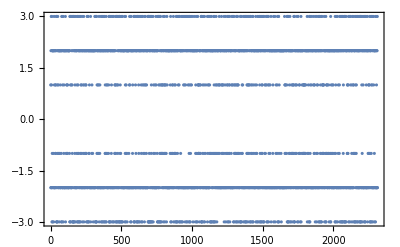

```mathematica
ListPlot[MapThread[(#1-#2)/(timestep/10^-4)&,rlbits],Frame->True,PlotRange->All]
```

#### Run length encoded data packets separated by run length >2 bits

```mathematica
rlruns=SplitBy[#,#>2&]&/@rlbits
```

{{{0.275,0.995,0.51,0.48,1.,0.99,0.5,0.5,0.51,0.485,0.99,0.985,1.005,0.495,0.5,0.985,0.995,0.98,0.99,0.985,0.99,0.98,0.995,0.98,0.995,0.985,0.995,0.985,0.995,0.995,0.51,0.49,0.51,0.49,1.005,0.495,0.495,0.985,1.,0.495,0.51,0.495,0.5,0.995,0.505,0.495,1.005,0.5,1.,0.99,0.505,0.995,1.005,0.5,1.005,0.995,0.505,1.005,1.005,0.5,1.005,0.995,0.505,0.99,0.505,0.49,0.995,0.985,0.99,0.98,1.005,0.495,0.495,0.995,0.505,0.49,0.995,0.99,0.51,0.485,0.995,0.98,0.995,0.985,0.995,0.98,0.995,0.985,1.005,0.495,0.505,0.495,0.51,0.5,0.495,0.98,0.99,0.98,0.995,0.985,0.99,0.985,0.995,0.98,0.995,0.98,1.,0.495,0.495,0.985,0.995,0.985,1.,0.5,0.505,0.5,0.49,0.995,0.505,0.49,0.995,0.98,1.005,0.99,0.51,0.995,1.,0.495,1.005,0.995,0.51,0.995,1.005,0.5,0.99},{14.95},{1.005,0.495,1.005,0.995,0.505,0.995,0.505,0.48,0.995,0.985,0.99,0.985,1.005,0.5,0.5,0.995,0.505,0.485,0.995,0.99,0.51,0.485,0.995,0.98,0.995,0.98,0.995,0.985,0.995,0.98,1.005,0.49,0.51,0.495,0.51,0.5,0.495,0.985,0.995,0.985,0.995,0.98,0.995,0.985,0.99,0.985,0.99,0.985,1.005,0.495,0.495,0.985,0.995,0.98,1.01,0.495,0.505,0.5,0.495,0.995,0.51,0.485,0.99,0.99,1.005,0.99,0.505,0.995,1.01,0.495,1.,0.99,0.505,0.995,1.01,0.495,0.99},{14.955},{1.005,0.495,1.005,0.99,0.505,0.995,0.51,0.485,0.995,0.985,0.995,0.98,1.005,0.5,0.495,0.995,0.505,0.49,0.995,0.995,0.51,0.485,0.995,0.985,0.99,0.985,0.995,0.98,0.995,0.98,1.005,0.495,0.51,0.5,0.505,0.495,0.49,0.985,0.995,0.985,0.995,0.98,0.99,0.985,0.995,0.98,0.995,0.98,1.005,0.495,0.495,0.985,0.995,0.98,1.,0.5,0.51,0.495,0.495,0.995,0.5,0.49,0.995,0.985,1.,0.99,0.505,0.995,1.01,0.495,1.005,0.99,0.51,0.995,1.,0.495,0.99},{54.78},{1.815,0.255,0.265,1.805,1.825,0.255,0.265,1.81,1.82,0.255,0.265,1.805,1.82,0.255,0.265,1.81,0.265,1.805,0.265,1.815,1.82,0.255,0.265,1.805,1.82,0.255,0.265,1.805,1.825,0.25,0.27,1.81,1.82,0.255,0.27},{16.745},{1.815,0.255,0.265,1.81,1.82,0.26,0.26,1.81,1.82,0.255,0.27,1.81,1.82,0.255,0.265,1.81,0.265,1.805,0.265,1.81,1.815,0.255,0.265,1.805,1.82,0.255,0.265,1.81,1.82,0.255,0.265,1.805,1.82,0.255,0.265},{41.645},{1.005,0.495,1.005,0.995,0.51,0.99,0.505,0.485,1.,0.985,0.995,0.98,0.995,0.98,1.,0.995,0.51,0.495,0.51,0.495,0.51,0.5,0.505,0.49,1.005,0.49,0.495,0.995,0.51,0.48,0.99,0.985,1.,0.495,0.505,0.5,0.505,0.495,0.495,0.995,0.505,0.49,0.995,0.98,1.005,0.5,0.49,0.98,0.995,0.99,0.51,0.49,0.51,0.485,1.01,0.495,0.495,0.99,0.505,0.485,0.995,0.99,0.51,0.5,0.505,0.49,0.99,0.985,1.01,0.495,0.5,0.985,0.995,0.985,0.995,0.985,0.995,0.98,0.995,0.985,0.995,0.985,0.99,0.98,0.995,0.99,0.505,0.5,0.505,0.49,1.,0.5,0.49,0.985,1.01,0.49,0.51,0.5,0.495,0.99,0.51,0.49,1.005,0.495,1.01,0.995,0.505,0.99,1.01,0.495,1.,0.995,0.505,1.005,1.01,0.49,1.005,0.995,0.505,0.99,0.505,0.485,1.,0.98,0.995,0.98,1.005,0.5,0.49,0.995,0.505,0.49,0.995,0.99,0.51,0.485,0.99,0.98,0.99,0.985,0.995,0.98,0.99,0.98,1.005,0.495,0.505,0.495,0.51,0.495,0.5,0.98,0.99,0.98,0.995,0.985,0.99,0.985,0.995,0.98,0.995,0.98,1.,0.495,0.495,0.98,1.,0.985,1.005,0.495,0.505,0.5,0.495,0.995,0.51,0.49,0.995,0.98,1.,0.995,0.51,0.99,1.,0.5,1.005,0.99,0.51,0.995,1.005,0.5,0.985},{14.95},{1.005,0.495,1.01,0.995,0.5,0.995,0.51,0.485,0.995,0.98,0.995,0.98,1.005,0.495,0.5,0.995,0.505,0.485,0.995,0.99,0.51,0.485,0.995,0.985,0.99,0.98,0.995,0.985,0.995,0.985,1.,0.5,0.51,0.495,0.51,0.495,0.5,0.985,0.995,0.985,0.99,0.985,1.,0.98,0.99,0.98,0.99,0.985,1.005,0.49,0.5,0.985,0.99,0.985,1.01,0.495,0.505,0.495,0.5,0.99,0.505,0.485,0.995,0.985,1.005,0.99,0.5,0.995,1.005,0.495,1.,0.995,0.505,0.995,1.01,0.495,0.99},{14.955},{1.005,0.5,1.005,0.995,0.51,0.995,0.505,0.49,0.99,0.98,0.99,0.985,1.005,0.495,0.495,0.99,0.5,0.49,0.995,0.99,0.51,0.49,0.995,0.98,0.99,0.98,0.995,0.98,0.995,0.985,1.005,0.5,0.505,0.5,0.505,0.5,0.495,0.985,0.99,0.98,0.995,0.985,0.995,0.985,0.99,0.98,0.995,0.985,1.005,0.495,0.5,0.985,0.995,0.985,1.005,0.495,0.51,0.495,0.5,0.99,0.505,0.485,0.995,0.985,1.005,0.995,0.51,0.995,1.,0.49,1.01,0.995,0.505,0.995,1.005,0.495,0.99},{54.78},{1.815,0.255,0.265,1.805,1.82,0.25,0.265,1.81,1.82,0.255,0.265,1.81,1.82,0.255,0.265,1.81,0.265,1.81,0.27,1.81,1.815,0.255,0.265,1.805,1.82,0.26,0.26,1.81,1.82,0.255,0.27,1.805,1.825,0.255,0.26},{16.735},{1.815,0.255,0.265,1.805,1.82,0.26,0.265,1.81,1.82,0.255,0.265,1.805,1.82,0.25,0.27,1.81,0.26,1.81,0.27,1.805,1.82,0.25,0.27,1.81,1.815,0.255,0.265,1.805,1.82,0.25,0.265,1.815,1.815,0.26,0.265},{41.635},{1.005,0.5,1.,0.995,0.505,0.995,0.5,0.49,0.99,0.985,0.995,0.98,0.995,0.985,0.995,0.995,0.51,0.5,0.505,0.5,0.505,0.5,0.51,0.485,1.005,0.5,0.495,0.99,0.51,0.49,0.995,0.985,1.005,0.5,0.505,0.495,0.505,0.495,0.5,0.995,0.5,0.485,0.99,0.98,1.,0.495,0.5,0.985,0.995,0.995,0.51,0.49,0.51,0.49,1.005,0.495,0.495,0.995,0.505,0.485,0.995,0.995,0.5,0.5,0.51,0.485,0.995,0.985,1.005,0.495,0.495,0.985,0.995,0.98,1.,0.985,0.99,0.98,0.995,0.99,0.995,0.985,0.99,0.98,1.,0.995,0.505,0.5,0.505,0.49,1.005,0.5,0.49,0.985,1.,0.49,0.51,0.5,0.495,0.99,0.51,0.5,1.005,0.49,1.01,0.995,0.505,0.995,1.005,0.495,1.005,0.99,0.505,1.01,1.005,0.49,1.01,0.99,0.505,0.99,0.51,0.485,0.995,0.98,0.99,0.985,1.005,0.495,0.5,0.995,0.505,0.49,0.995,0.995,0.51,0.49,0.995,0.985,0.995,0.98,0.995,0.98,0.995,0.98,1.005,0.495,0.505,0.495,0.505,0.495,0.5,0.985,0.995,0.985,1.,0.985,0.995,0.985,0.995,0.98,0.995,0.985,1.005,0.495,0.5,0.985,0.995,0.98,1.005,0.495,0.505,0.495,0.5,0.995,0.505,0.48,1.,0.985,1.005,0.995,0.51,0.99,1.005,0.5,1.005,0.995,0.51,0.995,1.005,0.495,0.99},{14.955},{1.005,0.495,1.,0.995,0.505,0.995,0.51,0.485,1.,0.985,0.995,0.98,1.,0.5,0.495,0.995,0.505,0.48,1.,0.99,0.5,0.49,0.99,0.985,0.995,0.985,0.995,0.985,0.99,0.985,1.005,0.495,0.51,0.495,0.505,0.495,0.495,0.98,0.995,0.98,0.995,0.985,0.995,0.98,1.,0.985,0.99,0.98,1.,0.5,0.49,0.985,0.995,0.985,1.005,0.5,0.505,0.495,0.5,0.995,0.505,0.485,0.995,0.985,1.005,0.995,0.5,1.,1.005,0.5,1.,0.995,0.505,1.,1.005,0.495,0.985},{14.955},{1.005,0.5,1.005,0.995,0.51,0.995,0.5,0.485,0.995,0.98,1.,0.98,1.005,0.49,0.5,0.99,0.505,0.485,0.995,0.99,0.505,0.49,0.995,0.985,0.99,0.985,1.,0.985,0.995,0.98,1.,0.5,0.5,0.495,0.505,0.49,0.5,0.985,0.995,0.98,0.995,0.99,0.995,0.985,0.99,0.98,0.995,0.985,1.005,0.495,0.5,0.985,0.995,0.98,1.005,0.495,0.505,0.5,0.495,0.99,0.51,0.485,1.,0.985,1.005,0.99,0.505,0.995,1.005,0.5,1.005,0.995,0.51,0.995,1.005,0.5,0.99},{54.775},{1.825,0.255,0.265,1.81,1.82,0.255,0.265,1.805,1.82,0.255,0.265,1.81,1.815,0.255,0.265,1.805,0.265,1.81,0.265,1.805,1.82,0.25,0.27,1.81,1.815,0.255,0.265,1.805,1.82,0.26,0.27,1.81,1.815,0.255,0.265},{16.735},{1.815,0.255,0.265,1.81,1.82,0.255,0.265,1.81,1.815,0.255,0.265,1.805,1.82,0.255,0.26,1.81,0.27,1.805,0.265,1.81,1.815,0.255,0.265,1.81,1.82,0.255,0.265,1.81,1.815,0.26,0.265,1.805,1.82,0.25,0.265},{41.645},{1.005,0.5,1.005,0.995,0.51,0.995,0.505,0.485,0.99,0.985,0.995,0.985,0.995,0.985,0.99,0.99,0.505,0.5,0.505,0.495,0.505,0.495,0.505,0.485,1.,0.5,0.49,0.995,0.505,0.49,0.99,0.98,1.005,0.5,0.505,0.495,0.51,0.495,0.495,0.99,0.505,0.49,0.995,0.98,1.,0.5,0.495,0.985,0.995,0.995,0.505,0.495,0.51,0.485,1.005,0.495,0.495,1.,0.505,0.485,0.995,0.99,0.505,0.495,0.51,0.485,0.99,0.985,1.005,0.495,0.5,0.985,0.99,0.99,0.995,0.985,0.995,0.985,1.,0.985,0.995,0.985,0.99,0.98,0.995,0.995,0.5,0.5,0.51,0.485,1.,0.5,0.495,0.98,1.005,0.495,0.505,0.5,0.495,1.,0.505,0.5,1.005,0.495,1.005,0.995,0.505,1.,1.005,0.495,1.01,0.995,0.51,1.005,1.005,0.495,1.005,0.99,0.51,0.99,0.505,0.49,0.995,0.985,0.995,0.99,1.005,0.495,0.5,0.995,0.505,0.485,0.995,0.99,0.51,0.49,0.99,0.98,0.995,0.98,0.995,0.98,0.995,0.985,1.01,0.495,0.51,0.495,0.51,0.5,0.495,0.99,0.995,0.985,0.99,0.985,0.995,0.98,0.995,0.98,0.995,0.98,1.005,0.495,0.495,0.985,0.995,0.98,1.005,0.495,0.51,0.495,0.5,0.99,0.505,0.485,1.,0.98,1.005,0.99,0.505,0.99,1.005,0.5,1.,0.995,0.51,0.995,1.,0.49,0.99},{14.955},{1.005,0.5,1.005,0.995,0.51,0.995,0.505,0.49,0.995,0.985,0.99,0.985,1.01,0.495,0.5,0.995,0.51,0.485,1.,0.995,0.505,0.485,0.995,0.98,0.99,0.985,0.99,0.985,0.99,0.985,1.,0.5,0.51,0.495,0.505,0.495,0.5,0.985,0.99,0.98,0.995,0.985,0.995,0.985,0.99,0.98,0.995,0.98,1.005,0.5,0.495,0.98,0.99,0.985,1.005,0.49,0.51,0.49,0.495,0.995,0.505,0.49,0.995,0.98,1.005,0.995,0.51,0.995,1.01,0.495,1.005,0.99,0.51,0.995,1.,0.5,0.985},{14.95},{1.01,0.49,1.005,0.995,0.505,0.995,0.51,0.49,0.995,0.98,0.995,0.985,1.01,0.495,0.5,0.995,0.51,0.485,0.995,1.,0.505,0.49,0.99,0.985,0.995,0.98,0.995,0.98,0.995,0.98,1.01,0.495,0.51,0.495,0.51,0.49,0.495,0.98,0.995,0.99,0.99,0.985,0.995,0.98,0.99,0.985,0.99,0.98,1.005,0.495,0.5,0.985,0.99,0.985,1.005,0.495,0.51,0.495,0.5,0.99,0.505,0.485,1.,0.985,1.,0.99,0.505,0.99,1.005,0.5,1.,0.99,0.51,0.995,1.005,0.5,0.99},{54.785},{1.815,0.255,0.27,1.805,1.82,0.255,0.27,1.81,1.815,0.255,0.265,1.805,1.82,0.26,0.265,1.81,0.265,1.81,0.265,1.81,1.815,0.255,0.265,1.81,1.82,0.255,0.265,1.81,1.815,0.255,0.27,1.805,1.82,0.255,0.265},{16.735},{1.82,0.255,0.265,1.81,1.82,0.26,0.26,1.81,1.815,0.255,0.265,1.81,1.82,0.255,0.26,1.81,0.265,1.805,0.265,1.805,1.82,0.255,0.27,1.805,1.82,0.25,0.265,1.81,1.815,0.26,0.265,1.81,1.82,0.255,0.265},{41.645},{1.005,0.5,1.005,0.995,0.51,0.995,0.505,0.485,0.995,0.98,0.995,0.98,0.995,0.985,0.995,0.99,0.51,0.495,0.505,0.49,0.505,0.5,0.505,0.49,1.005,0.49,0.495,0.995,0.505,0.48,1.,0.98,1.,0.5,0.505,0.5,0.505,0.495,0.49,0.995,0.505,0.49,0.995,0.98,1.005,0.5,0.49,0.98,0.995,0.99,0.505,0.495,0.51,0.485,1.01,0.495,0.5,0.995,0.505,0.49,0.995,0.99,0.505,0.5,0.505,0.49,0.995,0.98,1.01,0.495,0.495,0.985,0.995,0.98,0.99,0.985,0.995,0.985,0.995,0.98,0.99,0.99,0.995,0.985,0.995,0.995,0.51,0.5,0.505,0.485,1.005,0.5,0.495,0.985,1.005,0.5,0.505,0.495,0.5,0.995,0.51,0.495,1.005,0.5,1.,0.99,0.505,0.995,1.,0.5,1.005,0.99,0.505,1.005,1.005,0.5,1.,0.995,0.51,0.99,0.51,0.485,0.995,0.985,0.995,0.985,1.01,0.49,0.5,0.995,0.51,0.485,0.99,0.995,0.5,0.49,0.99,0.985,0.995,0.985,0.995,0.985,0.99,0.985,1.005,0.5,0.51,0.495,0.51,0.495,0.5,0.985,0.995,0.99,0.995,0.985,0.995,0.985,0.995,0.985,0.995,0.98,1.,0.5,0.49,0.99,0.99,0.985,1.,0.5,0.505,0.5,0.49,1.,0.505,0.49,0.995,0.985,1.005,1.,0.505,0.995,1.005,0.5,1.005,0.995,0.51,0.995,1.005,0.5,0.99},{14.95},{1.005,0.5,1.005,0.99,0.505,0.995,0.505,0.49,0.995,0.98,0.995,0.985,1.01,0.495,0.5,0.99,0.51,0.485,0.995,0.995,0.505,0.49,0.995,0.985,0.995,0.98,1.,0.98,0.99,0.98,1.005,0.495,0.505,0.495,0.505,0.495,0.5,0.985,0.995,0.985,1.,0.985,0.995,0.985,0.995,0.98,0.99,0.985,1.,0.495,0.495,0.985,0.995,0.98,1.01,0.495,0.505,0.495,0.5,0.995,0.505,0.485,0.995,0.985,1.005,0.99,0.51,0.995,1.,0.49,1.01,0.995,0.505,0.99,1.005,0.495,0.99},{14.955},{1.01,0.495,1.005,0.995,0.505,0.995,0.51,0.485,0.99,0.985,1.,0.98,1.005,0.5,0.49,0.995,0.51,0.485,0.995,0.99,0.51,0.485,0.99,0.99,0.995,0.98,0.99,0.985,0.99,0.985,1.005,0.5,0.505,0.5,0.505,0.5,0.495,0.985,0.995,0.985,0.995,0.985,0.995,0.98,0.995,0.98,0.995,0.985,1.005,0.5,0.495,0.98,0.995,0.98,1.005,0.5,0.505,0.5,0.495,0.995,0.505,0.485,0.99,0.985,1.,0.99,0.505,0.995,1.01,0.495,1.005,0.995,0.5,1.,1.005,0.49,0.99},{54.78},{1.815,0.255,0.265,1.805,1.82,0.26,0.265,1.81,1.82,0.25,0.265,1.81,1.815,0.26,0.265,1.805,0.27,1.805,0.265,1.81,1.815,0.255,0.27,1.805,1.82,0.255,0.26,1.81,1.815,0.255,0.27,1.81,1.82,0.255,0.265},{16.74},{1.82,0.255,0.265,1.805,1.82,0.25,0.27,1.81,1.815,0.255,0.265,1.81,1.82,0.25,0.265,1.81,0.265,1.81,0.265,1.81,1.82,0.25,0.265,1.805,1.82,0.255,0.26,1.81,1.82,0.255,0.265,1.81,1.82,0.255,0.26},{41.645},{1.01,0.495,1.005,0.995,0.505,0.995,0.51,0.485,0.99,0.985,0.995,0.985,0.99,0.98,0.995,0.99,0.505,0.495,0.505,0.495,0.51,0.495,0.51,0.485,1.,0.495,0.49,0.99,0.505,0.49,0.995,0.98,1.005,0.495,0.51,0.495,0.51,0.49,0.495,0.995,0.51,0.48,0.99,0.98,1.005,0.495,0.495,0.985,0.99,0.995,0.51,0.5,0.505,0.49,1.,0.5,0.495,0.995,0.51,0.49,0.99,0.995,0.51,0.495,0.505,0.485,0.995,0.985,1.005,0.495,0.5,0.98,0.995,0.98,0.995,0.985,0.995,0.98,1.,0.985,0.995,0.98,0.995,0.985,0.99,0.995,0.5,0.5,0.505,0.485,1.,0.495,0.5,0.98,1.005,0.495,0.505,0.5,0.495,0.995,0.505,0.495,1.005,0.495,1.,0.995,0.505,0.99,1.005,0.495,1.005,1.,0.505,1.,1.01,0.495,1.,0.995,0.505,0.99,0.51,0.485,1.,0.985,0.995,0.98,1.005,0.495,0.5,0.995,0.505,0.49,0.99,0.99,0.505,0.485,1.,0.98,0.995,0.985,0.995,0.985,0.995,0.98,1.,0.495,0.51,0.495,0.505,0.495,0.495,0.98,0.995,0.98,0.995,0.98,0.99,0.985,0.99,0.985,0.99,0.98,1.005,0.5,0.495,0.985,0.995,0.985,1.005,0.5,0.51,0.495,0.5,0.995,0.505,0.485,0.995,0.985,1.005,0.995,0.505,0.995,1.005,0.49,1.005,0.995,0.51,0.99,1.,0.5,0.99},{14.955},{1.005,0.5,1.005,0.995,0.51,0.99,0.505,0.49,0.995,0.985,0.995,0.98,1.,0.5,0.495,0.995,0.505,0.49,0.995,0.995,0.51,0.485,0.99,0.99,0.995,0.98,0.995,0.985,1.,0.98,1.005,0.495,0.505,0.5,0.51,0.495,0.5,0.985,0.99,0.985,0.99,0.985,0.995,0.985,0.99,0.985,0.995,0.985,1.,0.495,0.495,0.98,0.995,0.985,1.005,0.495,0.51,0.495,0.5,0.99,0.51,0.48,0.99,0.985,1.005,0.995,0.505,0.995,1.,0.495,1.005,0.995,0.505,0.99,1.005,0.295}},{{0.27,1.005,0.5,0.49,0.985,1.,0.495,0.51,0.495,0.5,0.98,0.99,0.995,0.51,0.49,0.995,0.985,0.99,0.98,0.99,0.98,0.995,0.985,0.99,0.98,0.995,0.99,0.995,0.985,1.005,0.5,0.5,0.5,0.495,1.,0.5,0.49,0.995,0.99,0.505,0.495,0.51,0.485,1.01,0.49,0.51,0.995,0.505,0.995,1.,0.49,1.01,0.995,0.505,1.,1.005,0.495,1.015,0.995,0.505,0.995,1.005,0.495,1.005,0.495,0.495,0.985,0.995,0.985,0.99,0.995,0.505,0.485,1.005,0.495,0.495,0.985,1.005,0.495,0.5,0.985,0.99,0.98,0.995,0.99,0.99,0.985,0.995,0.99,0.51,0.495,0.505,0.5,0.505,0.49,0.99,0.98,0.99,0.985,0.995,0.98,0.995,0.985,0.99,0.98,0.995,0.99,0.505,0.485,0.99,0.985,0.995,0.995,0.51,0.495,0.505,0.485,1.005,0.495,0.495,0.99,0.99,0.995,1.,0.5,1.005,0.99,0.505,0.995,1.005,0.5,1.005,0.995,0.505,0.98},{14.965},{0.99,0.51,0.99,1.005,0.5,1.005,0.49,0.495,0.98,0.995,0.985,0.995,0.995,0.51,0.485,1.005,0.5,0.49,0.985,1.005,0.495,0.5,0.98,0.995,0.98,0.995,0.985,0.995,0.98,0.995,0.99,0.505,0.5,0.505,0.5,0.505,0.49,0.995,0.985,0.995,0.98,0.995,0.985,0.995,0.98,0.995,0.98,0.995,0.995,0.5,0.49,0.995,0.98,0.995,0.995,0.51,0.495,0.505,0.49,1.005,0.495,0.5,0.98,0.995,0.995,1.005,0.495,1.005,0.995,0.51,0.99,1.,0.495,1.005,0.995,0.51,0.98},{14.96},{1.,0.5,0.995,1.,0.5,1.005,0.5,0.495,0.98,0.995,0.985,0.995,0.995,0.51,0.485,1.,0.5,0.5,0.985,1.005,0.495,0.5,0.985,0.99,0.985,0.995,0.985,0.99,0.985,0.99,0.995,0.505,0.5,0.505,0.5,0.5,0.485,0.99,0.985,1.,0.985,0.99,0.98,0.995,0.98,0.995,0.985,0.99,0.99,0.51,0.48,0.995,0.985,0.995,0.99,0.505,0.5,0.51,0.485,1.,0.495,0.5,0.985,0.995,0.99,1.,0.495,1.005,0.995,0.51,0.995,1.,0.5,1.005,0.99,0.505,0.98},{54.785},{1.81,0.265,0.255,1.815,1.815,0.26,0.255,1.82,1.81,0.27,0.255,1.815,1.81,0.265,0.255,1.82,0.255,1.815,0.255,1.825,1.805,0.27,0.255,1.815,1.81,0.265,0.25,1.82,1.81,0.265,0.255,1.825,1.805,0.27,0.26},{16.75},{1.81,0.265,0.255,1.82,1.81,0.265,0.255,1.82,1.81,0.265,0.26,1.815,1.815,0.265,0.25,1.825,0.255,1.815,0.255,1.815,1.81,0.265,0.255,1.815,1.81,0.265,0.255,1.82,1.805,0.27,0.255,1.815,1.81,0.265,0.25},{41.66},{0.995,0.505,0.99,1.005,0.5,1.005,0.495,0.495,0.99,0.995,0.985,0.99,0.98,0.995,0.99,1.005,0.495,0.51,0.5,0.505,0.5,0.505,0.5,0.495,0.995,0.505,0.485,1.005,0.495,0.495,0.98,0.99,0.995,0.505,0.495,0.505,0.5,0.505,0.485,1.005,0.495,0.5,0.985,0.99,0.995,0.505,0.485,0.99,0.98,1.005,0.495,0.505,0.5,0.495,0.995,0.51,0.48,1.005,0.495,0.495,0.985,1.,0.5,0.51,0.495,0.495,0.985,0.995,0.995,0.51,0.49,0.995,0.985,0.995,0.985,0.995,0.98,0.995,0.985,0.995,0.98,0.995,0.98,0.995,0.985,1.,0.495,0.51,0.495,0.495,0.995,0.505,0.485,0.995,0.995,0.505,0.5,0.505,0.49,1.,0.495,0.505,0.99,0.51,0.995,1.005,0.5,1.,0.995,0.51,0.99,1.,0.5,1.015,0.995,0.505,0.995,1.005,0.495,1.,0.49,0.5,0.985,0.995,0.98,0.995,0.995,0.505,0.485,1.005,0.495,0.495,0.985,1.005,0.495,0.5,0.98,0.99,0.98,0.995,0.98,0.995,0.98,0.99,0.99,0.51,0.495,0.505,0.5,0.505,0.49,0.99,0.98,0.99,0.985,0.995,0.98,0.995,0.985,0.99,0.98,0.995,0.99,0.5,0.49,0.99,0.985,1.,0.995,0.5,0.5,0.51,0.485,1.005,0.5,0.495,0.985,0.995,0.99,1.005,0.5,1.,0.99,0.51,0.995,1.,0.5,1.005,0.995,0.505,0.975},{14.96},{1.,0.505,0.995,1.005,0.495,1.005,0.5,0.495,0.98,0.995,0.985,0.99,0.99,0.51,0.49,1.005,0.495,0.495,0.985,1.,0.5,0.495,0.985,0.99,0.985,0.99,0.985,0.995,0.985,0.995,0.99,0.51,0.495,0.51,0.495,0.51,0.485,1.,0.985,0.995,0.98,0.995,0.985,0.99,0.985,0.99,0.98,0.99,0.995,0.505,0.49,0.995,0.98,0.995,0.995,0.51,0.495,0.505,0.485,1.005,0.49,0.5,0.985,0.995,0.99,1.,0.495,1.,0.995,0.51,0.99,1.005,0.495,1.005,0.995,0.51,0.98},{14.965},{0.995,0.51,0.995,1.005,0.495,1.005,0.5,0.495,0.98,0.995,0.98,0.995,0.99,0.51,0.48,1.,0.495,0.5,0.985,1.,0.5,0.495,0.985,0.99,0.985,0.99,0.985,0.99,0.98,1.,0.995,0.505,0.5,0.51,0.495,0.51,0.48,0.995,0.985,0.99,0.985,0.995,0.985,0.99,0.985,0.99,0.985,0.995,0.995,0.505,0.49,0.995,0.985,0.995,0.99,0.51,0.495,0.51,0.485,1.005,0.49,0.5,0.985,0.99,0.995,1.01,0.495,1.005,0.99,0.505,0.995,1.01,0.495,1.005,0.99,0.51,0.98},{54.785},{1.81,0.265,0.25,1.82,1.805,0.265,0.255,1.82,1.81,0.265,0.255,1.82,1.805,0.27,0.255,1.815,0.26,1.82,0.26,1.82,1.805,0.265,0.255,1.815,1.81,0.265,0.255,1.82,1.81,0.265,0.26,1.815,1.81,0.265,0.255},{16.745},{1.805,0.265,0.255,1.815,1.81,0.265,0.255,1.825,1.805,0.27,0.255,1.815,1.805,0.265,0.255,1.82,0.255,1.82,0.255,1.82,1.805,0.265,0.26,1.815,1.81,0.265,0.25,1.82,1.805,0.265,0.255,1.82,1.81,0.265,0.255},{41.65},{0.995,0.505,0.995,1.005,0.495,1.,0.495,0.495,0.985,0.995,0.985,0.99,0.98,1.,0.985,1.005,0.5,0.505,0.5,0.505,0.5,0.51,0.495,0.5,0.995,0.505,0.49,1.,0.5,0.495,0.99,0.995,0.995,0.505,0.495,0.51,0.495,0.505,0.485,1.005,0.495,0.495,0.98,0.99,0.99,0.505,0.49,0.995,0.985,1.005,0.5,0.5,0.5,0.5,0.995,0.505,0.485,1.005,0.495,0.495,0.985,1.,0.495,0.51,0.495,0.5,0.985,0.99,0.995,0.51,0.485,0.995,0.985,0.99,0.99,0.99,0.985,0.99,0.985,0.995,0.99,0.995,0.98,0.99,0.985,1.01,0.495,0.51,0.495,0.5,0.995,0.505,0.485,0.99,0.99,0.505,0.5,0.505,0.49,1.,0.5,0.505,0.995,0.505,0.995,1.01,0.495,1.005,0.99,0.51,0.995,1.,0.495,1.015,0.995,0.505,0.995,1.,0.5,1.,0.5,0.495,0.98,0.99,0.985,0.995,0.99,0.51,0.485,1.01,0.495,0.5,0.985,1.005,0.5,0.495,0.985,1.,0.985,0.99,0.985,0.99,0.98,0.995,0.995,0.505,0.495,0.505,0.49,0.51,0.49,0.995,0.985,0.995,0.985,0.995,0.99,0.995,0.985,0.99,0.98,0.995,1.,0.505,0.49,0.995,0.98,0.995,0.99,0.505,0.5,0.505,0.49,1.005,0.495,0.49,0.985,1.,0.995,1.005,0.495,1.005,0.995,0.51,0.995,1.005,0.495,1.005,1.,0.505,0.975},{14.965},{0.995,0.51,0.99,1.,0.5,1.005,0.495,0.5,0.985,0.995,0.985,0.995,0.99,0.505,0.49,1.005,0.495,0.49,0.985,1.,0.495,0.5,0.98,0.995,0.985,0.995,0.985,0.995,0.98,0.995,0.99,0.51,0.5,0.505,0.495,0.505,0.485,0.99,0.985,0.99,0.985,0.995,0.985,0.99,0.985,0.995,0.98,0.995,0.99,0.505,0.485,0.995,0.985,0.995,0.995,0.505,0.495,0.51,0.485,1.01,0.495,0.495,0.985,0.995,0.99,1.005,0.495,1.005,1.,0.505,0.995,1.,0.5,1.005,0.995,0.51,0.975},{14.965},{0.995,0.505,1.,1.005,0.5,1.,0.495,0.495,0.985,0.99,0.985,0.995,0.99,0.505,0.485,1.005,0.49,0.5,0.985,1.,0.495,0.495,0.99,0.995,0.98,0.995,0.985,0.995,0.985,0.995,0.99,0.505,0.495,0.505,0.49,0.505,0.49,0.995,0.985,0.99,0.985,0.995,0.985,0.995,0.985,0.99,0.985,0.995,0.995,0.505,0.49,0.995,0.985,0.99,0.99,0.51,0.495,0.505,0.49,1.,0.5,0.495,0.985,0.995,1.,1.,0.495,1.005,0.995,0.505,1.,1.005,0.495,1.01,0.995,0.505,0.98},{54.79},{1.815,0.26,0.255,1.825,1.805,0.27,0.255,1.815,1.81,0.26,0.255,1.825,1.805,0.265,0.255,1.815,0.255,1.815,0.255,1.82,1.805,0.265,0.26,1.815,1.81,0.265,0.25,1.82,1.81,0.265,0.26,1.825,1.805,0.265,0.255},{16.74},{1.81,0.265,0.25,1.82,1.815,0.26,0.255,1.825,1.805,0.265,0.255,1.815,1.81,0.26,0.255,1.82,0.26,1.815,0.255,1.815,1.81,0.265,0.255,1.82,1.805,0.265,0.26,1.815,1.81,0.27,0.255,1.815,1.81,0.26,0.255},{41.655},{0.995,0.51,0.995,1.005,0.495,1.005,0.5,0.49,0.985,0.995,0.985,0.99,0.99,0.995,0.98,1.,0.495,0.505,0.5,0.505,0.495,0.505,0.49,0.5,0.99,0.51,0.48,1.005,0.495,0.495,0.985,0.99,0.995,0.51,0.49,0.51,0.5,0.505,0.485,1.,0.495,0.495,0.985,0.99,0.995,0.505,0.49,0.995,0.98,1.01,0.495,0.505,0.495,0.5,0.995,0.505,0.485,1.005,0.5,0.49,0.99,1.,0.49,0.51,0.5,0.495,0.98,0.995,0.995,0.505,0.49,0.995,0.98,0.995,0.99,0.995,0.985,0.995,0.985,0.995,0.99,0.995,0.98,0.99,0.98,1.005,0.495,0.51,0.495,0.5,0.99,0.51,0.48,0.995,0.995,0.5,0.5,0.51,0.485,1.005,0.5,0.51,0.995,0.5,0.995,1.01,0.495,1.005,1.,0.505,0.995,1.01,0.495,1.015,1.,0.5,0.995,1.005,0.495,1.,0.5,0.495,0.99,0.995,0.985,0.995,0.995,0.51,0.49,1.005,0.495,0.495,0.985,1.,0.5,0.495,0.98,0.995,0.98,0.995,0.98,0.995,0.985,0.995,0.995,0.51,0.5,0.505,0.5,0.505,0.49,0.995,0.985,0.995,0.985,0.995,0.985,0.99,0.98,0.995,0.985,0.99,0.995,0.505,0.485,0.995,0.985,0.99,0.99,0.51,0.5,0.505,0.485,1.005,0.495,0.495,0.985,0.995,0.995,1.,0.49,1.005,0.995,0.505,0.995,1.005,0.5,1.,0.995,0.5,0.975},{14.97},{0.995,0.505,1.,1.005,0.495,1.005,0.5,0.495,0.99,0.995,0.98,0.995,0.995,0.51,0.49,1.005,0.495,0.5,0.985,1.005,0.5,0.49,0.985,0.995,0.98,0.995,0.98,0.99,0.985,0.995,0.99,0.51,0.495,0.51,0.49,0.51,0.49,0.99,0.985,0.99,0.985,0.995,0.985,0.995,0.98,0.99,0.985,0.99,0.995,0.505,0.49,0.99,0.98,0.995,0.99,0.505,0.5,0.5,0.485,1.,0.5,0.495,0.985,0.995,0.995,1.005,0.5,1.005,0.995,0.51,0.995,1.,0.5,1.005,0.99,0.51,0.975},{14.96},{0.995,0.505,0.99,1.005,0.5,1.005,0.5,0.495,0.985,0.995,0.985,0.995,0.995,0.51,0.49,1.005,0.495,0.5,0.985,1.005,0.5,0.495,0.985,0.995,0.985,0.99,0.98,0.995,0.985,0.99,0.995,0.51,0.5,0.505,0.495,0.505,0.485,0.99,0.985,0.995,0.985,0.995,0.985,0.99,0.98,0.99,0.985,0.99,0.995,0.505,0.485,0.995,0.985,0.995,0.99,0.51,0.5,0.505,0.485,1.005,0.495,0.495,0.985,0.995,0.995,1.,0.49,1.005,0.995,0.505,0.995,1.,0.5,1.005,0.995,0.51,0.98},{54.79},{1.81,0.265,0.26,1.815,1.81,0.265,0.255,1.825,1.805,0.265,0.255,1.815,1.81,0.27,0.255,1.82,0.255,1.82,0.255,1.815,1.81,0.265,0.255,1.82,1.805,0.27,0.255,1.82,1.805,0.265,0.26,1.815,1.81,0.265,0.25},{16.75},{1.81,0.265,0.255,1.82,1.81,0.265,0.255,1.82,1.805,0.265,0.255,1.82,1.81,0.26,0.255,1.82,0.25,1.82,0.255,1.815,1.81,0.265,0.255,1.82,1.805,0.265,0.255,1.815,1.81,0.27,0.255,1.82,1.81,0.265,0.255},{41.655},{0.995,0.51,0.995,1.005,0.5,1.,0.495,0.5,0.985,0.99,0.985,0.99,0.985,0.995,0.985,1.,0.5,0.505,0.495,0.5,0.495,0.51,0.495,0.5,0.995,0.5,0.485,1.005,0.495,0.49,0.985,0.99,0.995,0.505,0.5,0.51,0.495,0.5,0.485,1.005,0.495,0.5,0.985,0.99,0.995,0.505,0.485,0.99,0.98,1.005,0.495,0.505,0.495,0.5,0.995,0.51,0.485,1.01,0.495,0.5,0.985,1.,0.495,0.505,0.5,0.495,0.985,0.995,0.995,0.505,0.485,0.995,0.985,0.995,0.98,0.995,0.985,0.99,0.99,0.99,0.98,0.995,0.985,1.,0.985,1.005,0.5,0.505,0.5,0.49,1.,0.505,0.49,0.995,0.995,0.51,0.49,0.51,0.485,1.01,0.495,0.51,0.995,0.505,0.995,1.,0.495,1.005,0.99,0.505,1.,1.,0.495,1.015,0.995,0.505,0.995,1.005,0.495,1.,0.5,0.5,0.985,0.995,0.985,0.995,0.995,0.505,0.49,1.005,0.5,0.495,0.98,1.,0.495,0.495,0.985,0.995,0.985,0.99,0.985,1.,0.98,0.995,0.995,0.51,0.495,0.51,0.5,0.505,0.49,0.995,0.985,0.995,0.99,0.995,0.985,0.995,0.985,0.99,0.985,0.99,0.995,0.505,0.485,0.995,0.985,0.99,0.995,0.51,0.495,0.505,0.485,1.005,0.5,0.5,0.985,0.995,0.995,1.005,0.5,1.005,0.995,0.51,0.995,1.005,0.5,1.005,0.995,0.51,0.975},{14.965},{0.995,0.505,0.995,1.,0.495,1.005,0.5,0.495,0.985,0.995,0.985,0.995,1.,0.505,0.485,1.005,0.495,0.5,0.985,1.,0.5,0.5,0.985,0.995,0.985,0.99,0.985,0.99,0.985,0.99,0.995,0.505,0.495,0.505,0.495,0.505,0.49,0.995,0.985,0.995,0.985,0.995,0.99,0.995,0.985,0.99,0.98,0.99,0.995,0.5,0.49,0.995,0.985,0.99,0.995,0.51,0.495,0.505,0.49,1.005,0.495,0.495,0.985,0.99,0.995,1.005,0.495,1.005,0.995,0.5,1.,1.,0.5,1.,0.995,0.505,0.98},{14.965},{0.995,0.51,0.995,1.005,0.495,1.005,0.495,0.5,0.98,0.995,0.985,0.995,0.995,0.505,0.485,1.005,0.5,0.49,0.985,1.005,0.495,0.5,0.98,1.,0.98,0.99,0.985,0.995,0.98,0.99,1.,0.505,0.5,0.505,0.5,0.51,0.485,0.99,0.99,0.995,0.98,0.995,0.985,0.995,0.985,0.99,0.985,0.995,0.995,0.505,0.485,0.995,0.98,0.995,0.995,0.505,0.5,0.51,0.485,1.,0.5,0.49,0.985,0.995,0.99,1.,0.495,1.005,1.,0.505,0.995,1.,0.495,1.005,0.995,0.505,0.98},{54.79},{1.805,0.265,0.255,1.815,1.81,0.265,0.255,1.825,1.805,0.265,0.255,1.815,1.81,0.27,0.255,1.815,0.26,1.815,0.255,1.815,1.81,0.265,0.26,1.815,1.81,0.26,0.255,1.82,1.805,0.265,0.26,1.82,1.81,0.265,0.255},{16.75},{1.81,0.26,0.255,1.82,1.805,0.265,0.26,1.815,1.81,0.265,0.255,1.82,1.805,0.265,0.255,1.82,0.255,1.82,0.255,1.82,1.805,0.265,0.255,1.815,1.81,0.26,0.255,1.82,1.81,0.265,0.255,1.82,1.81,0.26,0.255},{41.655},{0.995,0.51,0.995,1.005,0.495,1.005,0.495,0.5,0.98,0.995,0.98,0.995,0.98,0.995,0.98,1.005,0.495,0.505,0.495,0.505,0.495,0.51,0.495,0.5,0.99,0.5,0.485,1.,0.495,0.5,0.985,0.99,0.99,0.51,0.495,0.51,0.495,0.505,0.485,1.005,0.495,0.495,0.98,0.99,0.99,0.51,0.485,0.995,0.98,1.005,0.5,0.51,0.495,0.495,0.995,0.505,0.49,1.005,0.5,0.495,0.985,1.005,0.495,0.51,0.495,0.495,0.985,0.995,0.99,0.51,0.49,0.99,0.985,0.99,0.98,0.995,0.99,0.99,0.985,0.995,0.985,0.995,0.985,0.995,0.98,1.,0.495,0.51,0.495,0.495,0.99,0.505,0.485,0.995,0.99,0.505,0.5,0.505,0.49,1.005,0.495,0.5,0.995,0.51,0.99,1.,0.495,1.005,0.99,0.51,0.995,1.005,0.5,1.01,0.995,0.51,0.99,1.,0.5,1.,0.5,0.495,0.985,1.,0.985,0.99,0.99,0.51,0.49,1.005,0.495,0.5,0.98,1.,0.495,0.495,0.985,0.995,0.985,0.995,0.98,0.995,0.985,0.995,0.99,0.505,0.495,0.51,0.49,0.51,0.48,0.995,0.985,0.99,0.98,0.99,0.985,0.995,0.98,0.99,0.98,0.995,0.995,0.51,0.48,0.995,0.99,0.995,0.995,0.51,0.5,0.505,0.485,1.01,0.495,0.495,0.985,0.995,0.99,1.01,0.49,1.01,0.995,0.5,0.995,1.005,0.495,1.,0.995,0.51,0.98},{14.965},{0.995,0.51,0.995,1.005,0.495,1.005,0.495,0.5,0.985,0.99,0.985,0.99,0.995,0.505,0.49,1.005,0.495,0.495,0.99,1.005,0.495,0.5,0.98,0.995,0.985,0.995,0.985,0.995,0.985,0.995,0.995,0.5,0.5,0.51,0.495,0.51,0.485,0.995,0.985,0.995,0.98,0.995,0.98,1.,0.98,0.995,0.98,0.995,0.995,0.505,0.485,0.99,0.985,0.99,0.995,0.51,0.5,0.505,0.49,1.,0.495,0.495,0.98,0.995,0.995,1.005,0.49,1.005,0.995,0.505,0.995,1.005,0.495,1.,0.99,0.305}}}

```mathematica
Dimensions[rlruns]
```

{2,53}

```mathematica
Map[Length,rlruns,{2}]
```

{{135,1,77,1,77,1,35,1,35,1,191,1,77,1,77,1,35,1,35,1,191,1,77,1,77,1,35,1,35,1,191,1,77,1,77,1,35,1,35,1,191,1,77,1,77,1,35,1,35,1,191,1,76},{135,1,77,1,77,1,35,1,35,1,191,1,77,1,77,1,35,1,35,1,191,1,77,1,77,1,35,1,35,1,191,1,77,1,77,1,35,1,35,1,191,1,77,1,77,1,35,1,35,1,191,1,76}}

#### Length of packet separators in 100μs bit frames

```mathematica
TableForm[Transpose[Select[#,Length[#]≤1&]&/@rlruns]]
```

14.95 | 14.965
14.955 | 14.96
54.78 | 54.785
16.745 | 16.75
41.645 | 41.66
14.95 | 14.96
14.955 | 14.965
54.78 | 54.785
16.735 | 16.745
41.635 | 41.65
14.955 | 14.965
14.955 | 14.965
54.775 | 54.79
16.735 | 16.74
41.645 | 41.655
14.955 | 14.97
14.95 | 14.96
54.785 | 54.79
16.735 | 16.75
41.645 | 41.655
14.95 | 14.965
14.955 | 14.965
54.78 | 54.79
16.74 | 16.75
41.645 | 41.655
14.955 | 14.965

### Run length encoded packets

Display number of runs per packet

```mathematica
TableForm[Transpose[Map[Length,packetruns=Select[#,Length[#]>1&]&/@rlruns,{2}]]]
```

135 | 135
77 | 77
77 | 77
35 | 35
35 | 35
191 | 191
77 | 77
77 | 77
35 | 35
35 | 35
191 | 191
77 | 77
77 | 77
35 | 35
35 | 35
191 | 191
77 | 77
77 | 77
35 | 35
35 | 35
191 | 191
77 | 77
77 | 77
35 | 35
35 | 35
191 | 191
76 | 76

### Runs in 25μs time unit multiples

```mathematica
RoundRunTime=Round[4#]&
```

Round[4 #1]&

```mathematica
MatrixForm[Transpose[mmruns=RoundRunTime[Select[#,Length[#]==35&]&/@packetruns]]]
```

((7
1
1
7
7
1
1
7
7
1
1
7
7
1
1
7
1
7
1
7
7
1
1
7
7
1
1
7
7
1
1
7
7
1
1) | (7
1
1
7
7
1
1
7
7
1
1
7
7
1
1
7
1
7
1
7
7
1
1
7
7
1
1
7
7
1
1
7
7
1
1)
(7
1
1
7
7
1
1
7
7
1
1
7
7
1
1
7
1
7
1
7
7
1
1
7
7
1
1
7
7
1
1
7
7
1
1) | (7
1
1
7
7
1
1
7
7
1
1
7
7
1
1
7
1
7
1
7
7
1
1
7
7
1
1
7
7
1
1
7
7
1
1)
(7
1
1
7
7
1
1
7
7
1
1
7
7
1
1
7
1
7
1
7
7
1
1
7
7
1
1
7
7
1
1
7
7
1
1) | (7
1
1
7
7
1
1
7
7
1
1
7
7
1
1
7
1
7
1
7
7
1
1
7
7
1
1
7
7
1
1
7
7
1
1)
(7
1
1
7
7
1
1
7
7
1
1
7
7
1
1
7
1
7
1
7
7
1
1
7
7
1
1
7
7
1
1
7
7
1
1) | (7
1
1
7
7
1
1
7
7
1
1
7
7
1
1
7
1
7
1
7
7
1
1
7
7
1
1
7
7
1
1
7
7
1
1)
(7
1
1
7
7
1
1
7
7
1
1
7
7
1
1
7
1
7
1
7
7
1
1
7
7
1
1
7
7
1
1
7
7
1
1) | (7
1
1
7
7
1
1
7
7
1
1
7
7
1
1
7
1
7
1
7
7
1
1
7
7
1
1
7
7
1
1
7
7
1
1)
(7
1
1
7
7
1
1
7
7
1
1
7
7
1
1
7
1
7
1
7
7
1
1
7
7
1
1
7
7
1
1
7
7
1
1) | (7
1
1
7
7
1
1
7
7
1
1
7
7
1
1
7
1
7
1
7
7
1
1
7
7
1
1
7
7
1
1
7
7
1
1)
(7
1
1
7
7
1
1
7
7
1
1
7
7
1
1
7
1
7
1
7
7
1
1
7
7
1
1
7
7
1
1
7
7
1
1) | (7
1
1
7
7
1
1
7
7
1
1
7
7
1
1
7
1
7
1
7
7
1
1
7
7
1
1
7
7
1
1
7
7
1
1)
(7
1
1
7
7
1
1
7
7
1
1
7
7
1
1
7
1
7
1
7
7
1
1
7
7
1
1
7
7
1
1
7
7
1
1) | (7
1
1
7
7
1
1
7
7
1
1
7
7
1
1
7
1
7
1
7
7
1
1
7
7
1
1
7
7
1
1
7
7
1
1)
(7
1
1
7
7
1
1
7
7
1
1
7
7
1
1
7
1
7
1
7
7
1
1
7
7
1
1
7
7
1
1
7
7
1
1) | (7
1
1
7
7
1
1
7
7
1
1
7
7
1
1
7
1
7
1
7
7
1
1
7
7
1
1
7
7
1
1
7
7
1
1)
(7
1
1
7
7
1
1
7
7
1
1
7
7
1
1
7
1
7
1
7
7
1
1
7
7
1
1
7
7
1
1
7
7
1
1) | (7
1
1
7
7
1
1
7
7
1
1
7
7
1
1
7
1
7
1
7
7
1
1
7
7
1
1
7
7
1
1
7
7
1
1))

```mathematica
MatrixForm[Transpose[mediumruns=RoundRunTime[Select[#,Length[#]==77&]&/@packetruns]]]
```

((4
2
4
4
2
4
2
2
4
4
4
4
4
2
2
4
2
2
4
4
2
2
4
4
4
4
4
4
4
4
4
2
2
2
2
2
2
4
4
4
4
4
4
4
4
4
4
4
4
2
2
4
4
4
4
2
2
2
2
4
2
2
4
4
4
4
2
4
4
2
4
4
2
4
4
2
4) | (4
2
4
4
2
4
2
2
4
4
4
4
4
2
2
4
2
2
4
4
2
2
4
4
4
4
4
4
4
4
4
2
2
2
2
2
2
4
4
4
4
4
4
4
4
4
4
4
4
2
2
4
4
4
4
2
2
2
2
4
2
2
4
4
4
4
2
4
4
2
4
4
2
4
4
2
4)
(4
2
4
4
2
4
2
2
4
4
4
4
4
2
2
4
2
2
4
4
2
2
4
4
4
4
4
4
4
4
4
2
2
2
2
2
2
4
4
4
4
4
4
4
4
4
4
4
4
2
2
4
4
4
4
2
2
2
2
4
2
2
4
4
4
4
2
4
4
2
4
4
2
4
4
2
4) | (4
2
4
4
2
4
2
2
4
4
4
4
4
2
2
4
2
2
4
4
2
2
4
4
4
4
4
4
4
4
4
2
2
2
2
2
2
4
4
4
4
4
4
4
4
4
4
4
4
2
2
4
4
4
4
2
2
2
2
4
2
2
4
4
4
4
2
4
4
2
4
4
2
4
4
2
4)
(4
2
4
4
2
4
2
2
4
4
4
4
4
2
2
4
2
2
4
4
2
2
4
4
4
4
4
4
4
4
4
2
2
2
2
2
2
4
4
4
4
4
4
4
4
4
4
4
4
2
2
4
4
4
4
2
2
2
2
4
2
2
4
4
4
4
2
4
4
2
4
4
2
4
4
2
4) | (4
2
4
4
2
4
2
2
4
4
4
4
4
2
2
4
2
2
4
4
2
2
4
4
4
4
4
4
4
4
4
2
2
2
2
2
2
4
4
4
4
4
4
4
4
4
4
4
4
2
2
4
4
4
4
2
2
2
2
4
2
2
4
4
4
4
2
4
4
2
4
4
2
4
4
2
4)
(4
2
4
4
2
4
2
2
4
4
4
4
4
2
2
4
2
2
4
4
2
2
4
4
4
4
4
4
4
4
4
2
2
2
2
2
2
4
4
4
4
4
4
4
4
4
4
4
4
2
2
4
4
4
4
2
2
2
2
4
2
2
4
4
4
4
2
4
4
2
4
4
2
4
4
2
4) | (4
2
4
4
2
4
2
2
4
4
4
4
4
2
2
4
2
2
4
4
2
2
4
4
4
4
4
4
4
4
4
2
2
2
2
2
2
4
4
4
4
4
4
4
4
4
4
4
4
2
2
4
4
4
4
2
2
2
2
4
2
2
4
4
4
4
2
4
4
2
4
4
2
4
4
2
4)
(4
2
4
4
2
4
2
2
4
4
4
4
4
2
2
4
2
2
4
4
2
2
4
4
4
4
4
4
4
4
4
2
2
2
2
2
2
4
4
4
4
4
4
4
4
4
4
4
4
2
2
4
4
4
4
2
2
2
2
4
2
2
4
4
4
4
2
4
4
2
4
4
2
4
4
2
4) | (4
2
4
4
2
4
2
2
4
4
4
4
4
2
2
4
2
2
4
4
2
2
4
4
4
4
4
4
4
4
4
2
2
2
2
2
2
4
4
4
4
4
4
4
4
4
4
4
4
2
2
4
4
4
4
2
2
2
2
4
2
2
4
4
4
4
2
4
4
2
4
4
2
4
4
2
4)
(4
2
4
4
2
4
2
2
4
4
4
4
4
2
2
4
2
2
4
4
2
2
4
4
4
4
4
4
4
4
4
2
2
2
2
2
2
4
4
4
4
4
4
4
4
4
4
4
4
2
2
4
4
4
4
2
2
2
2
4
2
2
4
4
4
4
2
4
4
2
4
4
2
4
4
2
4) | (4
2
4
4
2
4
2
2
4
4
4
4
4
2
2
4
2
2
4
4
2
2
4
4
4
4
4
4
4
4
4
2
2
2
2
2
2
4
4
4
4
4
4
4
4
4
4
4
4
2
2
4
4
4
4
2
2
2
2
4
2
2
4
4
4
4
2
4
4
2
4
4
2
4
4
2
4)
(4
2
4
4
2
4
2
2
4
4
4
4
4
2
2
4
2
2
4
4
2
2
4
4
4
4
4
4
4
4
4
2
2
2
2
2
2
4
4
4
4
4
4
4
4
4
4
4
4
2
2
4
4
4
4
2
2
2
2
4
2
2
4
4
4
4
2
4
4
2
4
4
2
4
4
2
4) | (4
2
4
4
2
4
2
2
4
4
4
4
4
2
2
4
2
2
4
4
2
2
4
4
4
4
4
4
4
4
4
2
2
2
2
2
2
4
4
4
4
4
4
4
4
4
4
4
4
2
2
4
4
4
4
2
2
2
2
4
2
2
4
4
4
4
2
4
4
2
4
4
2
4
4
2
4)
(4
2
4
4
2
4
2
2
4
4
4
4
4
2
2
4
2
2
4
4
2
2
4
4
4
4
4
4
4
4
4
2
2
2
2
2
2
4
4
4
4
4
4
4
4
4
4
4
4
2
2
4
4
4
4
2
2
2
2
4
2
2
4
4
4
4
2
4
4
2
4
4
2
4
4
2
4) | (4
2
4
4
2
4
2
2
4
4
4
4
4
2
2
4
2
2
4
4
2
2
4
4
4
4
4
4
4
4
4
2
2
2
2
2
2
4
4
4
4
4
4
4
4
4
4
4
4
2
2
4
4
4
4
2
2
2
2
4
2
2
4
4
4
4
2
4
4
2
4
4
2
4
4
2
4)
(4
2
4
4
2
4
2
2
4
4
4
4
4
2
2
4
2
2
4
4
2
2
4
4
4
4
4
4
4
4
4
2
2
2
2
2
2
4
4
4
4
4
4
4
4
4
4
4
4
2
2
4
4
4
4
2
2
2
2
4
2
2
4
4
4
4
2
4
4
2
4
4
2
4
4
2
4) | (4
2
4
4
2
4
2
2
4
4
4
4
4
2
2
4
2
2
4
4
2
2
4
4
4
4
4
4
4
4
4
2
2
2
2
2
2
4
4
4
4
4
4
4
4
4
4
4
4
2
2
4
4
4
4
2
2
2
2
4
2
2
4
4
4
4
2
4
4
2
4
4
2
4
4
2
4)
(4
2
4
4
2
4
2
2
4
4
4
4
4
2
2
4
2
2
4
4
2
2
4
4
4
4
4
4
4
4
4
2
2
2
2
2
2
4
4
4
4
4
4
4
4
4
4
4
4
2
2
4
4
4
4
2
2
2
2
4
2
2
4
4
4
4
2
4
4
2
4
4
2
4
4
2
4) | (4
2
4
4
2
4
2
2
4
4
4
4
4
2
2
4
2
2
4
4
2
2
4
4
4
4
4
4
4
4
4
2
2
2
2
2
2
4
4
4
4
4
4
4
4
4
4
4
4
2
2
4
4
4
4
2
2
2
2
4
2
2
4
4
4
4
2
4
4
2
4
4
2
4
4
2
4))

```mathematica
MatrixForm[Transpose[longruns=RoundRunTime[Select[#,Length[#]==191&]&/@packetruns]]]
```

((4
2
4
4
2
4
2
2
4
4
4
4
4
4
4
4
2
2
2
2
2
2
2
2
4
2
2
4
2
2
4
4
4
2
2
2
2
2
2
4
2
2
4
4
4
2
2
4
4
4
2
2
2
2
4
2
2
4
2
2
4
4
2
2
2
2
4
4
4
2
2
4
4
4
4
4
4
4
4
4
4
4
4
4
4
4
2
2
2
2
4
2
2
4
4
2
2
2
2
4
2
2
4
2
4
4
2
4
4
2
4
4
2
4
4
2
4
4
2
4
2
2
4
4
4
4
4
2
2
4
2
2
4
4
2
2
4
4
4
4
4
4
4
4
4
2
2
2
2
2
2
4
4
4
4
4
4
4
4
4
4
4
4
2
2
4
4
4
4
2
2
2
2
4
2
2
4
4
4
4
2
4
4
2
4
4
2
4
4
2
4) | (4
2
4
4
2
4
2
2
4
4
4
4
4
4
4
4
2
2
2
2
2
2
2
2
4
2
2
4
2
2
4
4
4
2
2
2
2
2
2
4
2
2
4
4
4
2
2
4
4
4
2
2
2
2
4
2
2
4
2
2
4
4
2
2
2
2
4
4
4
2
2
4
4
4
4
4
4
4
4
4
4
4
4
4
4
4
2
2
2
2
4
2
2
4
4
2
2
2
2
4
2
2
4
2
4
4
2
4
4
2
4
4
2
4
4
2
4
4
2
4
2
2
4
4
4
4
4
2
2
4
2
2
4
4
2
2
4
4
4
4
4
4
4
4
4
2
2
2
2
2
2
4
4
4
4
4
4
4
4
4
4
4
4
2
2
4
4
4
4
2
2
2
2
4
2
2
4
4
4
4
2
4
4
2
4
4
2
4
4
2
4)
(4
2
4
4
2
4
2
2
4
4
4
4
4
4
4
4
2
2
2
2
2
2
2
2
4
2
2
4
2
2
4
4
4
2
2
2
2
2
2
4
2
2
4
4
4
2
2
4
4
4
2
2
2
2
4
2
2
4
2
2
4
4
2
2
2
2
4
4
4
2
2
4
4
4
4
4
4
4
4
4
4
4
4
4
4
4
2
2
2
2
4
2
2
4
4
2
2
2
2
4
2
2
4
2
4
4
2
4
4
2
4
4
2
4
4
2
4
4
2
4
2
2
4
4
4
4
4
2
2
4
2
2
4
4
2
2
4
4
4
4
4
4
4
4
4
2
2
2
2
2
2
4
4
4
4
4
4
4
4
4
4
4
4
2
2
4
4
4
4
2
2
2
2
4
2
2
4
4
4
4
2
4
4
2
4
4
2
4
4
2
4) | (4
2
4
4
2
4
2
2
4
4
4
4
4
4
4
4
2
2
2
2
2
2
2
2
4
2
2
4
2
2
4
4
4
2
2
2
2
2
2
4
2
2
4
4
4
2
2
4
4
4
2
2
2
2
4
2
2
4
2
2
4
4
2
2
2
2
4
4
4
2
2
4
4
4
4
4
4
4
4
4
4
4
4
4
4
4
2
2
2
2
4
2
2
4
4
2
2
2
2
4
2
2
4
2
4
4
2
4
4
2
4
4
2
4
4
2
4
4
2
4
2
2
4
4
4
4
4
2
2
4
2
2
4
4
2
2
4
4
4
4
4
4
4
4
4
2
2
2
2
2
2
4
4
4
4
4
4
4
4
4
4
4
4
2
2
4
4
4
4
2
2
2
2
4
2
2
4
4
4
4
2
4
4
2
4
4
2
4
4
2
4)
(4
2
4
4
2
4
2
2
4
4
4
4
4
4
4
4
2
2
2
2
2
2
2
2
4
2
2
4
2
2
4
4
4
2
2
2
2
2
2
4
2
2
4
4
4
2
2
4
4
4
2
2
2
2
4
2
2
4
2
2
4
4
2
2
2
2
4
4
4
2
2
4
4
4
4
4
4
4
4
4
4
4
4
4
4
4
2
2
2
2
4
2
2
4
4
2
2
2
2
4
2
2
4
2
4
4
2
4
4
2
4
4
2
4
4
2
4
4
2
4
2
2
4
4
4
4
4
2
2
4
2
2
4
4
2
2
4
4
4
4
4
4
4
4
4
2
2
2
2
2
2
4
4
4
4
4
4
4
4
4
4
4
4
2
2
4
4
4
4
2
2
2
2
4
2
2
4
4
4
4
2
4
4
2
4
4
2
4
4
2
4) | (4
2
4
4
2
4
2
2
4
4
4
4
4
4
4
4
2
2
2
2
2
2
2
2
4
2
2
4
2
2
4
4
4
2
2
2
2
2
2
4
2
2
4
4
4
2
2
4
4
4
2
2
2
2
4
2
2
4
2
2
4
4
2
2
2
2
4
4
4
2
2
4
4
4
4
4
4
4
4
4
4
4
4
4
4
4
2
2
2
2
4
2
2
4
4
2
2
2
2
4
2
2
4
2
4
4
2
4
4
2
4
4
2
4
4
2
4
4
2
4
2
2
4
4
4
4
4
2
2
4
2
2
4
4
2
2
4
4
4
4
4
4
4
4
4
2
2
2
2
2
2
4
4
4
4
4
4
4
4
4
4
4
4
2
2
4
4
4
4
2
2
2
2
4
2
2
4
4
4
4
2
4
4
2
4
4
2
4
4
2
4)
(4
2
4
4
2
4
2
2
4
4
4
4
4
4
4
4
2
2
2
2
2
2
2
2
4
2
2
4
2
2
4
4
4
2
2
2
2
2
2
4
2
2
4
4
4
2
2
4
4
4
2
2
2
2
4
2
2
4
2
2
4
4
2
2
2
2
4
4
4
2
2
4
4
4
4
4
4
4
4
4
4
4
4
4
4
4
2
2
2
2
4
2
2
4
4
2
2
2
2
4
2
2
4
2
4
4
2
4
4
2
4
4
2
4
4
2
4
4
2
4
2
2
4
4
4
4
4
2
2
4
2
2
4
4
2
2
4
4
4
4
4
4
4
4
4
2
2
2
2
2
2
4
4
4
4
4
4
4
4
4
4
4
4
2
2
4
4
4
4
2
2
2
2
4
2
2
4
4
4
4
2
4
4
2
4
4
2
4
4
2
4) | (4
2
4
4
2
4
2
2
4
4
4
4
4
4
4
4
2
2
2
2
2
2
2
2
4
2
2
4
2
2
4
4
4
2
2
2
2
2
2
4
2
2
4
4
4
2
2
4
4
4
2
2
2
2
4
2
2
4
2
2
4
4
2
2
2
2
4
4
4
2
2
4
4
4
4
4
4
4
4
4
4
4
4
4
4
4
2
2
2
2
4
2
2
4
4
2
2
2
2
4
2
2
4
2
4
4
2
4
4
2
4
4
2
4
4
2
4
4
2
4
2
2
4
4
4
4
4
2
2
4
2
2
4
4
2
2
4
4
4
4
4
4
4
4
4
2
2
2
2
2
2
4
4
4
4
4
4
4
4
4
4
4
4
2
2
4
4
4
4
2
2
2
2
4
2
2
4
4
4
4
2
4
4
2
4
4
2
4
4
2
4)
(4
2
4
4
2
4
2
2
4
4
4
4
4
4
4
4
2
2
2
2
2
2
2
2
4
2
2
4
2
2
4
4
4
2
2
2
2
2
2
4
2
2
4
4
4
2
2
4
4
4
2
2
2
2
4
2
2
4
2
2
4
4
2
2
2
2
4
4
4
2
2
4
4
4
4
4
4
4
4
4
4
4
4
4
4
4
2
2
2
2
4
2
2
4
4
2
2
2
2
4
2
2
4
2
4
4
2
4
4
2
4
4
2
4
4
2
4
4
2
4
2
2
4
4
4
4
4
2
2
4
2
2
4
4
2
2
4
4
4
4
4
4
4
4
4
2
2
2
2
2
2
4
4
4
4
4
4
4
4
4
4
4
4
2
2
4
4
4
4
2
2
2
2
4
2
2
4
4
4
4
2
4
4
2
4
4
2
4
4
2
4) | (4
2
4
4
2
4
2
2
4
4
4
4
4
4
4
4
2
2
2
2
2
2
2
2
4
2
2
4
2
2
4
4
4
2
2
2
2
2
2
4
2
2
4
4
4
2
2
4
4
4
2
2
2
2
4
2
2
4
2
2
4
4
2
2
2
2
4
4
4
2
2
4
4
4
4
4
4
4
4
4
4
4
4
4
4
4
2
2
2
2
4
2
2
4
4
2
2
2
2
4
2
2
4
2
4
4
2
4
4
2
4
4
2
4
4
2
4
4
2
4
2
2
4
4
4
4
4
2
2
4
2
2
4
4
2
2
4
4
4
4
4
4
4
4
4
2
2
2
2
2
2
4
4
4
4
4
4
4
4
4
4
4
4
2
2
4
4
4
4
2
2
2
2
4
2
2
4
4
4
4
2
4
4
2
4
4
2
4
4
2
4))

```mathematica
truncruns=RoundRunTime[Select[#,Function[l,And@@(l≠#&/@{1,35,77,191})][Length[#]]&]&/@packetruns]
```

{{{1,4,2,2,4,4,2,2,2,2,4,4,4,2,2,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,2,2,2,2,4,2,2,4,4,2,2,2,2,4,2,2,4,2,4,4,2,4,4,2,4,4,2,4,4,2,4,4,2,4,2,2,4,4,4,4,4,2,2,4,2,2,4,4,2,2,4,4,4,4,4,4,4,4,4,2,2,2,2,2,2,4,4,4,4,4,4,4,4,4,4,4,4,2,2,4,4,4,4,2,2,2,2,4,2,2,4,4,4,4,2,4,4,2,4,4,2,4,4,2,4},{4,2,4,4,2,4,2,2,4,4,4,4,4,2,2,4,2,2,4,4,2,2,4,4,4,4,4,4,4,4,4,2,2,2,2,2,2,4,4,4,4,4,4,4,4,4,4,4,4,2,2,4,4,4,4,2,2,2,2,4,2,2,4,4,4,4,2,4,4,2,4,4,2,4,4,1}},{{1,4,2,2,4,4,2,2,2,2,4,4,4,2,2,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,2,2,2,2,4,2,2,4,4,2,2,2,2,4,2,2,4,2,4,4,2,4,4,2,4,4,2,4,4,2,4,4,2,4,2,2,4,4,4,4,4,2,2,4,2,2,4,4,2,2,4,4,4,4,4,4,4,4,4,2,2,2,2,2,2,4,4,4,4,4,4,4,4,4,4,4,4,2,2,4,4,4,4,2,2,2,2,4,2,2,4,4,4,4,2,4,4,2,4,4,2,4,4,2,4},{4,2,4,4,2,4,2,2,4,4,4,4,4,2,2,4,2,2,4,4,2,2,4,4,4,4,4,4,4,4,4,2,2,2,2,2,2,4,4,4,4,4,4,4,4,4,4,4,4,2,2,4,4,4,4,2,2,2,2,4,2,2,4,4,4,4,2,4,4,2,4,4,2,4,4,1}}}

```mathematica
Function[l,And@@(l≠#&/@{1,35,77,191})][35]
```

False

## Parse runs

### Shotgun mfx parser

```mathematica
mfxparser=Function[{in,out},
If[Length[in]≥6 ∧ {4,2,4,4,2,4}==Take[in,6],{Drop[in,6],Append[out,SYNC]},
If[Length[in]≥2∧{2,2}==Take[in,2],{Drop[in,2],Append[out,1]},
If[{4}==Take[in,1],{Drop[in,1],Append[out,0]},{Drop[in,1],Append[out,⚠]}]]]
]
```

Function[{in,out},If[Length[in]≥6&&{4,2,4,4,2,4}==Take[in,6],{Drop[in,6],Append[out,SYNC]},If[Length[in]≥2&&{2,2}==Take[in,2],{Drop[in,2],Append[out,1]},If[{4}==Take[in,1],{Drop[in,1],Append[out,0]},{Drop[in,1],Append[out,⚠]}]]]]

#### Parse by iteration over run length encoded input

```mathematica
NestWhile[mfxparser@@#&,{mediumruns⟦1,1⟧,{}},Length[First[#]]>0&]
```

{{},{SYNC,1,0,0,0,0,0,1,0,1,0,0,1,0,0,0,0,0,0,0,0,0,1,1,1,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,1,1,0,1,0,0,0,SYNC,SYNC}}

### Shotgun MM parser

```mathematica
MMparser=Function[{in,out},
If[Length[in]≥2,
Which[{1,7}==Take[in,2],{Drop[in,2],Append[out,0]},
{7,1}==Take[in,2],{Drop[in,2],Append[out,1]},
True,{Drop[in,1],Append[out,⚠]}],
If[Length[in]==1,Which[{1}==Take[in,1],{Drop[in,1],Append[out,0]},{7}==Take[in,1],{Drop[in,1],Append[out,1]},True,{Drop[in,1],Append[out,⚠]}],{Drop[in,1],Append[out,⚠]}]]
]
```

Function[{in,out},If[Length[in]≥2,Which[{1,7}==Take[in,2],{Drop[in,2],Append[out,0]},{7,1}==Take[in,2],{Drop[in,2],Append[out,1]},True,{Drop[in,1],Append[out,⚠]}],If[Length[in]==1,Which[{1}==Take[in,1],{Drop[in,1],Append[out,0]},{7}==Take[in,1],{Drop[in,1],Append[out,1]},True,{Drop[in,1],Append[out,⚠]}],{Drop[in,1],Append[out,⚠]}]]]

#### Parse by iteration over run length encoded input

```mathematica
NestWhile[MMparser@@#&,{mmruns⟦1,1⟧,{}},Length[First[#]]>0&]
```

{{},{1,0,1,0,1,0,1,0,0,0,1,0,1,0,1,0,1,0}}

### Apply parsers

#### Parse over medium length runs

```mathematica
Map[Last[NestWhile[mfxparser@@#&,{#,{}},Length[First[#]]>0&]]&,mediumruns,{2}]
```

{{{SYNC,1,0,0,0,0,0,1,0,1,0,0,1,0,0,0,0,0,0,0,0,0,1,1,1,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,1,1,0,1,0,0,0,SYNC,SYNC},{SYNC,1,0,0,0,0,0,1,0,1,0,0,1,0,0,0,0,0,0,0,0,0,1,1,1,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,1,1,0,1,0,0,0,SYNC,SYNC},{SYNC,1,0,0,0,0,0,1,0,1,0,0,1,0,0,0,0,0,0,0,0,0,1,1,1,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,1,1,0,1,0,0,0,SYNC,SYNC},{SYNC,1,0,0,0,0,0,1,0,1,0,0,1,0,0,0,0,0,0,0,0,0,1,1,1,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,1,1,0,1,0,0,0,SYNC,SYNC},{SYNC,1,0,0,0,0,0,1,0,1,0,0,1,0,0,0,0,0,0,0,0,0,1,1,1,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,1,1,0,1,0,0,0,SYNC,SYNC},{SYNC,1,0,0,0,0,0,1,0,1,0,0,1,0,0,0,0,0,0,0,0,0,1,1,1,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,1,1,0,1,0,0,0,SYNC,SYNC},{SYNC,1,0,0,0,0,0,1,0,1,0,0,1,0,0,0,0,0,0,0,0,0,1,1,1,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,1,1,0,1,0,0,0,SYNC,SYNC},{SYNC,1,0,0,0,0,0,1,0,1,0,0,1,0,0,0,0,0,0,0,0,0,1,1,1,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,1,1,0,1,0,0,0,SYNC,SYNC},{SYNC,1,0,0,0,0,0,1,0,1,0,0,1,0,0,0,0,0,0,0,0,0,1,1,1,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,1,1,0,1,0,0,0,SYNC,SYNC},{SYNC,1,0,0,0,0,0,1,0,1,0,0,1,0,0,0,0,0,0,0,0,0,1,1,1,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,1,1,0,1,0,0,0,SYNC,SYNC}},{{SYNC,1,0,0,0,0,0,1,0,1,0,0,1,0,0,0,0,0,0,0,0,0,1,1,1,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,1,1,0,1,0,0,0,SYNC,SYNC},{SYNC,1,0,0,0,0,0,1,0,1,0,0,1,0,0,0,0,0,0,0,0,0,1,1,1,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,1,1,0,1,0,0,0,SYNC,SYNC},{SYNC,1,0,0,0,0,0,1,0,1,0,0,1,0,0,0,0,0,0,0,0,0,1,1,1,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,1,1,0,1,0,0,0,SYNC,SYNC},{SYNC,1,0,0,0,0,0,1,0,1,0,0,1,0,0,0,0,0,0,0,0,0,1,1,1,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,1,1,0,1,0,0,0,SYNC,SYNC},{SYNC,1,0,0,0,0,0,1,0,1,0,0,1,0,0,0,0,0,0,0,0,0,1,1,1,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,1,1,0,1,0,0,0,SYNC,SYNC},{SYNC,1,0,0,0,0,0,1,0,1,0,0,1,0,0,0,0,0,0,0,0,0,1,1,1,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,1,1,0,1,0,0,0,SYNC,SYNC},{SYNC,1,0,0,0,0,0,1,0,1,0,0,1,0,0,0,0,0,0,0,0,0,1,1,1,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,1,1,0,1,0,0,0,SYNC,SYNC},{SYNC,1,0,0,0,0,0,1,0,1,0,0,1,0,0,0,0,0,0,0,0,0,1,1,1,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,1,1,0,1,0,0,0,SYNC,SYNC},{SYNC,1,0,0,0,0,0,1,0,1,0,0,1,0,0,0,0,0,0,0,0,0,1,1,1,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,1,1,0,1,0,0,0,SYNC,SYNC},{SYNC,1,0,0,0,0,0,1,0,1,0,0,1,0,0,0,0,0,0,0,0,0,1,1,1,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,1,1,0,1,0,0,0,SYNC,SYNC}}}

```mathematica
Map[Last[NestWhile[MMparser@@#&,{#,{}},Length[First[#]]>0&]]&,mediumruns,{2}]
```

{{{⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠},{⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠},{⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠},{⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠},{⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠},{⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠},{⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠},{⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠},{⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠},{⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠}},{{⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠},{⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠},{⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠},{⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠},{⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠},{⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠},{⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠},{⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠},{⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠},{⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠}}}

#### Parse over long runs

```mathematica
Map[Last[NestWhile[mfxparser@@#&,{#,{}},Length[First[#]]>0&]]&,longruns,{2}]
```

{{{SYNC,1,0,0,0,0,0,0,0,0,1,1,1,1,0,1,0,1,0,0,0,1,1,1,0,1,0,0,0,1,0,0,0,1,1,0,1,0,1,0,0,1,1,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,0,1,0,0,1,1,0,1,SYNC,SYNC,SYNC,1,0,0,0,0,0,1,0,1,0,0,1,0,0,0,0,0,0,0,0,0,1,1,1,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,1,1,0,1,0,0,0,SYNC,SYNC},{SYNC,1,0,0,0,0,0,0,0,0,1,1,1,1,0,1,0,1,0,0,0,1,1,1,0,1,0,0,0,1,0,0,0,1,1,0,1,0,1,0,0,1,1,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,0,1,0,0,1,1,0,1,SYNC,SYNC,SYNC,1,0,0,0,0,0,1,0,1,0,0,1,0,0,0,0,0,0,0,0,0,1,1,1,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,1,1,0,1,0,0,0,SYNC,SYNC},{SYNC,1,0,0,0,0,0,0,0,0,1,1,1,1,0,1,0,1,0,0,0,1,1,1,0,1,0,0,0,1,0,0,0,1,1,0,1,0,1,0,0,1,1,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,0,1,0,0,1,1,0,1,SYNC,SYNC,SYNC,1,0,0,0,0,0,1,0,1,0,0,1,0,0,0,0,0,0,0,0,0,1,1,1,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,1,1,0,1,0,0,0,SYNC,SYNC},{SYNC,1,0,0,0,0,0,0,0,0,1,1,1,1,0,1,0,1,0,0,0,1,1,1,0,1,0,0,0,1,0,0,0,1,1,0,1,0,1,0,0,1,1,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,0,1,0,0,1,1,0,1,SYNC,SYNC,SYNC,1,0,0,0,0,0,1,0,1,0,0,1,0,0,0,0,0,0,0,0,0,1,1,1,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,1,1,0,1,0,0,0,SYNC,SYNC},{SYNC,1,0,0,0,0,0,0,0,0,1,1,1,1,0,1,0,1,0,0,0,1,1,1,0,1,0,0,0,1,0,0,0,1,1,0,1,0,1,0,0,1,1,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,0,1,0,0,1,1,0,1,SYNC,SYNC,SYNC,1,0,0,0,0,0,1,0,1,0,0,1,0,0,0,0,0,0,0,0,0,1,1,1,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,1,1,0,1,0,0,0,SYNC,SYNC}},{{SYNC,1,0,0,0,0,0,0,0,0,1,1,1,1,0,1,0,1,0,0,0,1,1,1,0,1,0,0,0,1,0,0,0,1,1,0,1,0,1,0,0,1,1,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,0,1,0,0,1,1,0,1,SYNC,SYNC,SYNC,1,0,0,0,0,0,1,0,1,0,0,1,0,0,0,0,0,0,0,0,0,1,1,1,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,1,1,0,1,0,0,0,SYNC,SYNC},{SYNC,1,0,0,0,0,0,0,0,0,1,1,1,1,0,1,0,1,0,0,0,1,1,1,0,1,0,0,0,1,0,0,0,1,1,0,1,0,1,0,0,1,1,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,0,1,0,0,1,1,0,1,SYNC,SYNC,SYNC,1,0,0,0,0,0,1,0,1,0,0,1,0,0,0,0,0,0,0,0,0,1,1,1,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,1,1,0,1,0,0,0,SYNC,SYNC},{SYNC,1,0,0,0,0,0,0,0,0,1,1,1,1,0,1,0,1,0,0,0,1,1,1,0,1,0,0,0,1,0,0,0,1,1,0,1,0,1,0,0,1,1,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,0,1,0,0,1,1,0,1,SYNC,SYNC,SYNC,1,0,0,0,0,0,1,0,1,0,0,1,0,0,0,0,0,0,0,0,0,1,1,1,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,1,1,0,1,0,0,0,SYNC,SYNC},{SYNC,1,0,0,0,0,0,0,0,0,1,1,1,1,0,1,0,1,0,0,0,1,1,1,0,1,0,0,0,1,0,0,0,1,1,0,1,0,1,0,0,1,1,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,0,1,0,0,1,1,0,1,SYNC,SYNC,SYNC,1,0,0,0,0,0,1,0,1,0,0,1,0,0,0,0,0,0,0,0,0,1,1,1,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,1,1,0,1,0,0,0,SYNC,SYNC},{SYNC,1,0,0,0,0,0,0,0,0,1,1,1,1,0,1,0,1,0,0,0,1,1,1,0,1,0,0,0,1,0,0,0,1,1,0,1,0,1,0,0,1,1,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,0,1,0,0,1,1,0,1,SYNC,SYNC,SYNC,1,0,0,0,0,0,1,0,1,0,0,1,0,0,0,0,0,0,0,0,0,1,1,1,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,1,1,0,1,0,0,0,SYNC,SYNC}}}

```mathematica
Map[Last[NestWhile[MMparser@@#&,{#,{}},Length[First[#]]>0&]]&,longruns,{2}]
```

{{{⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠},{⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠},{⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠},{⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠},{⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠}},{{⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠},{⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠},{⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠},{⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠},{⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠}}}

#### Parse over MM runs

```mathematica
Map[Last[NestWhile[mfxparser@@#&,{#,{}},Length[First[#]]>0&]]&,mmruns,{2}]
```

{{{⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠},{⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠},{⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠},{⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠},{⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠},{⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠},{⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠},{⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠},{⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠},{⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠}},{{⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠},{⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠},{⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠},{⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠},{⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠},{⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠},{⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠},{⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠},{⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠},{⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠}}}

```mathematica
Map[Last[NestWhile[MMparser@@#&,{#,{}},Length[First[#]]>0&]]&,mmruns,{2}]
```

{{{1,0,1,0,1,0,1,0,0,0,1,0,1,0,1,0,1,0},{1,0,1,0,1,0,1,0,0,0,1,0,1,0,1,0,1,0},{1,0,1,0,1,0,1,0,0,0,1,0,1,0,1,0,1,0},{1,0,1,0,1,0,1,0,0,0,1,0,1,0,1,0,1,0},{1,0,1,0,1,0,1,0,0,0,1,0,1,0,1,0,1,0},{1,0,1,0,1,0,1,0,0,0,1,0,1,0,1,0,1,0},{1,0,1,0,1,0,1,0,0,0,1,0,1,0,1,0,1,0},{1,0,1,0,1,0,1,0,0,0,1,0,1,0,1,0,1,0},{1,0,1,0,1,0,1,0,0,0,1,0,1,0,1,0,1,0},{1,0,1,0,1,0,1,0,0,0,1,0,1,0,1,0,1,0}},{{1,0,1,0,1,0,1,0,0,0,1,0,1,0,1,0,1,0},{1,0,1,0,1,0,1,0,0,0,1,0,1,0,1,0,1,0},{1,0,1,0,1,0,1,0,0,0,1,0,1,0,1,0,1,0},{1,0,1,0,1,0,1,0,0,0,1,0,1,0,1,0,1,0},{1,0,1,0,1,0,1,0,0,0,1,0,1,0,1,0,1,0},{1,0,1,0,1,0,1,0,0,0,1,0,1,0,1,0,1,0},{1,0,1,0,1,0,1,0,0,0,1,0,1,0,1,0,1,0},{1,0,1,0,1,0,1,0,0,0,1,0,1,0,1,0,1,0},{1,0,1,0,1,0,1,0,0,0,1,0,1,0,1,0,1,0},{1,0,1,0,1,0,1,0,0,0,1,0,1,0,1,0,1,0}}}

#### Parse over truncated runs

```mathematica
Map[Last[NestWhile[mfxparser@@#&,{#,{}},Length[First[#]]>0&]]&,truncruns,{2}]
```

{{{⚠,0,1,0,0,1,1,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,0,1,0,0,1,1,0,1,SYNC,SYNC,SYNC,1,0,0,0,0,0,1,0,1,0,0,1,0,0,0,0,0,0,0,0,0,1,1,1,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,1,1,0,1,0,0,0,SYNC,SYNC},{SYNC,1,0,0,0,0,0,1,0,1,0,0,1,0,0,0,0,0,0,0,0,0,1,1,1,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,1,1,0,1,0,0,0,SYNC,0,⚠,0,0,⚠}},{{⚠,0,1,0,0,1,1,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,0,1,0,0,1,1,0,1,SYNC,SYNC,SYNC,1,0,0,0,0,0,1,0,1,0,0,1,0,0,0,0,0,0,0,0,0,1,1,1,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,1,1,0,1,0,0,0,SYNC,SYNC},{SYNC,1,0,0,0,0,0,1,0,1,0,0,1,0,0,0,0,0,0,0,0,0,1,1,1,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,1,1,0,1,0,0,0,SYNC,0,⚠,0,0,⚠}}}

```mathematica
Map[Last[NestWhile[MMparser@@#&,{#,{}},Length[First[#]]>0&]]&,truncruns,{2}]
```

{{{⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠},{⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,0}},{{⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠},{⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,0}}}